```mathematica
(*TBH FORMATION*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
(*ttherm[mx_?NumericQ,sigma_?NumericQ,T_]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*sigma*kb*T);*)
```

```mathematica
auni[100,sigmasat]
```

2.87365×10^23

```mathematica
agen[100,sigmasat,0.1]
```

2.86342×10^23

```mathematica
tage=6.69*10^9*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
totcapgen[100,sigmasat,0.01]
```

4.69646×10^40

```mathematica
Tc[mx_,sigma_,T_,rho_]:=(2*π)/mx*(((rho/0.4*totcapuni[mx,sigma])/(4/3*π*rth[mx,T]^3))/(2*2.6124))^(2/3)*(1.98*10^-14*10^-2)^2*1.16*10^13;(*in K*)
```

```mathematica
Tc[10^3,10^-49,2.1*10^6,10^3]
```

1.04273×10^8

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27);
(*NxBEC[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*2.612*((mx*T*8.62*10^-14)/(2*π))^1.5*(5.62*10^15)^3;*)
Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
NchFermion[mx_?NumericQ]:=Mpl^3/mx^3;
```

```mathematica
initbhmass[mx_]:=mx*Max[Nself[mx,2.1*10^6],NchBoson[mx]];(*in units of GeV*)
```

```mathematica
bhradius[mx_]:=2*GN*initbhmass[mx]*1.98*10^-14;(*in cm*)
```

```mathematica
bhradius[10^6]
```

1.82044×10^26 GN

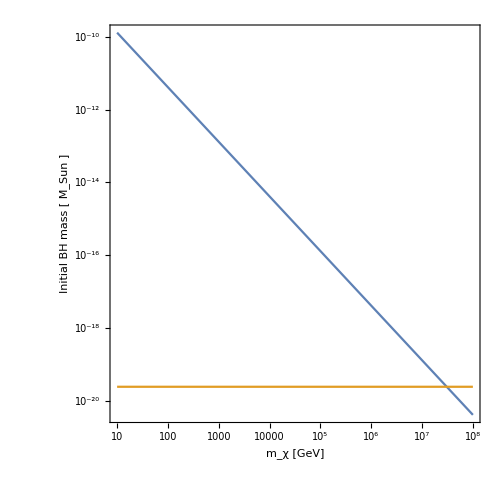

```mathematica
LogLogPlot[{initbhmass[mx]*1/(5.62*10^23*2*10^33),mcrit*1/(5.62*10^23*2*10^33)},{mx,10,10^8},Frame->True,AspectRatio->1,ImageSize->500,FrameTicksStyle->20,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["Initial BH mass [ M_Sun ]",FontSize->20]}]
```

```mathematica
GN=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
cns=0.17;
λ=0.25;
```

```mathematica
mcrit=1/GN*(cns^3/(74*π*4*π*λ*ρ*5.62*10^26*(1.98*10^-16)^3))^0.25;(*critical mass for BH evaporation in GeV*)
```

```mathematica
mcrit
```

2.71619×10^37

```mathematica
τcollapse[mx_?NumericQ,T_?NumericQ]:=cns^3/(4*π*λ*ρ*10^-3*5.62*10^23*(1.98*10^-14)^3*GN^2*mx*Max[Nself[mx,T],NchBoson[mx]])*6.58*10^-25*1/(3.15*10^7);(*in year, time required to consume the host star*)
```

```mathematica
τtrans[ρ_?NumericQ,mx_?NumericQ,T_?NumericQ,sigma_?NumericQ]:=1/(ρ/0.4*auni[mx,sigma])*Max[Nself[mx,T],NchBoson[mx]]*1/(3.15*10^7)+τcollapse[mx,T];
(*in year, time required to transmute, first term presents time required to capture enough DM particles to achieve the BH foramtion criterion, second term presents time required to consume the host star*)
```

```mathematica
τtrans[10^3,10^4,2.1*10^6,10^-50]
```

4.57859×10^7

```mathematica
Max[Nself[10^4,2.1*10^6],NchBoson[10^4]]
```

4.59708×10^38

```mathematica
FindRoot[10^x*Max[Nself[10^x,2.1*10^6],NchBoson[10^x]]==mcrit,{x,0}]//Quiet(*Without BEC*)
```

{x→7.48568}

```mathematica
FindRoot[10^x*Max[Nself[10^x,2.1*10^6],NchFermion[10^x]]==mcrit,{x,0}]//Quiet(*Without BEC*)
```

{x→9.91315}

```mathematica
10^7.48568
```

3.05971×10^7

```mathematica
10^9.91315
```

8.18748×10^9

```mathematica
myticks={{{{-44,"10^-40",{0.020,0}},{Log10[9*10^-45],"",{0.010,0}},{Log10[8*10^-45],"",{0.010,0}},{Log10[7*10^-45],"",{0.010,0}},{Log10[6*10^-45],"",{0.010,0}},{Log10[5*10^-45],"",{0.010,0}},{Log10[4*10^-45],"",{0.010,0}},{Log10[3*10^-45],"",{0.010,0}},{Log10[2*10^-45],"",{0.010,0}},{-45,"10^-41",{0.020,0}},{Log10[9*10^-46],"",{0.010,0}},{Log10[8*10^-46],"",{0.010,0}},{Log10[7*10^-46],"",{0.010,0}},{Log10[6*10^-46],"",{0.010,0}},{Log10[5*10^-46],"",{0.010,0}},{Log10[4*10^-46],"",{0.010,0}},{Log10[3*10^-46],"",{0.010,0}},{Log10[2*10^-46],"",{0.010,0}},{-46,"",{0.020,0}},{Log10[9*10^-47],"",{0.010,0}},{Log10[8*10^-47],"",{0.010,0}},{Log10[7*10^-47],"",{0.010,0}},{Log10[6*10^-47],"",{0.010,0}},{Log10[5*10^-47],"",{0.010,0}},{Log10[4*10^-47],"",{0.010,0}},{Log10[3*10^-47],"",{0.010,0}},{Log10[2*10^-47],"",{0.010,0}},{-47,"10^-43",{0.020,0}},{Log10[9*10^-48],"",{0.010,0}},{Log10[8*10^-48],"",{0.010,0}},{Log10[7*10^-48],"",{0.010,0}},{Log10[6*10^-48],"",{0.010,0}},{Log10[5*10^-48],"",{0.010,0}},{Log10[4*10^-48],"",{0.010,0}},{Log10[3*10^-48],"",{0.010,0}},{Log10[2*10^-48],"",{0.010,0}},{-48,"",{0.020,0}},{Log10[9*10^-49],"",{0.010,0}},{Log10[8*10^-49],"",{0.010,0}},{Log10[7*10^-49],"",{0.010,0}},{Log10[6*10^-49],"",{0.010,0}},{Log10[5*10^-49],"",{0.010,0}},{Log10[4*10^-49],"",{0.010,0}},{Log10[3*10^-49],"",{0.010,0}},{Log10[2*10^-49],"",{0.010,0}},{-49,"10^-45",{0.020,0}},{Log10[9*10^-50],"",{0.010,0}},{Log10[8*10^-50],"",{0.010,0}},{Log10[7*10^-50],"",{0.010,0}},{Log10[6*10^-50],"",{0.010,0}},{Log10[5*10^-50],"",{0.010,0}},{Log10[4*10^-50],"",{0.010,0}},{Log10[3*10^-50],"",{0.010,0}},{Log10[2*10^-50],"",{0.010,0}},{-50,"",{0.020,0}},{Log10[9*10^-51],"",{0.010,0}},{Log10[8*10^-51],"",{0.010,0}},{Log10[7*10^-51],"",{0.010,0}},{Log10[6*10^-51],"",{0.010,0}},{Log10[5*10^-51],"",{0.010,0}},{Log10[4*10^-51],"",{0.010,0}},{Log10[3*10^-51],"",{0.010,0}},{Log10[2*10^-51],"",{0.010,0}},{-51,"10^-47",{0.020,0}},{Log10[9*10^-52],"",{0.010,0}},{Log10[8*10^-52],"",{0.010,0}},{Log10[7*10^-52],"",{0.010,0}},{Log10[6*10^-52],"",{0.010,0}},{Log10[5*10^-52],"",{0.010,0}},{Log10[4*10^-52],"",{0.010,0}},{Log10[3*10^-52],"",{0.010,0}},{Log10[2*10^-52],"",{0.010,0}},{-52,"",{0.020,0}},{Log10[9*10^-53],"",{0.010,0}},{Log10[8*10^-53],"",{0.010,0}},{Log10[7*10^-53],"",{0.010,0}},{Log10[6*10^-53],"",{0.010,0}},{Log10[5*10^-53],"",{0.010,0}},{Log10[4*10^-53],"",{0.010,0}},{Log10[3*10^-53],"",{0.010,0}},{Log10[2*10^-53],"",{0.010,0}},{-53,"10^-49",{0.020,0}},{Log10[9*10^-54],"",{0.010,0}},{Log10[8*10^-54],"",{0.010,0}},{Log10[7*10^-54],"",{0.010,0}},{Log10[6*10^-54],"",{0.010,0}},{Log10[5*10^-54],"",{0.010,0}},{Log10[4*10^-54],"",{0.010,0}},{Log10[3*10^-54],"",{0.010,0}},{Log10[2*10^-54],"",{0.010,0}},{-54,"",{0.020,0}},{Log10[9*10^-55],"",{0.010,0}},{Log10[8*10^-55],"",{0.010,0}},{Log10[7*10^-55],"",{0.010,0}},{Log10[6*10^-55],"",{0.010,0}},{Log10[5*10^-55],"",{0.010,0}},{Log10[4*10^-55],"",{0.010,0}},{Log10[3*10^-55],"",{0.010,0}},{Log10[2*10^-55],"",{0.010,0}},{-55,"10^-51",{0.020,0}},{Log10[9*10^-56],"",{0.010,0}},{Log10[8*10^-56],"",{0.010,0}},{Log10[7*10^-56],"",{0.010,0}},{Log10[6*10^-56],"",{0.010,0}},{Log10[5*10^-56],"",{0.010,0}},{Log10[4*10^-56],"",{0.010,0}},{Log10[3*10^-56],"",{0.010,0}},{Log10[2*10^-56],"",{0.010,0}},{-56,"",{0.020,0}},{Log10[9*10^-57],"",{0.010,0}},{Log10[8*10^-57],"",{0.010,0}},{Log10[7*10^-57],"",{0.010,0}},{Log10[6*10^-57],"",{0.010,0}},{Log10[5*10^-57],"",{0.010,0}},{Log10[4*10^-57],"",{0.010,0}},{Log10[3*10^-57],"",{0.010,0}},{Log10[2*10^-57],"",{0.010,0}},{-57,"10^-53",{0.020,0}}},None},{{{0,"1",{0.020,0}},{Log10[2],"",{0.010,0}},{Log10[3],"",{0.010,0}},{Log10[4],"",{0.010,0}},{Log10[5],"",{0.010,0}},{Log10[6],"",{0.010,0}},{Log10[7],"",{0.010,0}},{Log10[8],"",{0.010,0}},{Log10[9],"",{0.010,0}},{1,"10",{0.020,0}},{Log10[20],"",{0.010,0}},{Log10[30],"",{0.010,0}},{Log10[40],"",{0.010,0}},{Log10[50],"",{0.010,0}},{Log10[60],"",{0.010,0}},{Log10[70],"",{0.010,0}},{Log10[80],"",{0.010,0}},{Log10[90],"",{0.010,0}},{2,"",{0.020,0}},{Log10[200],"",{0.010,0}},{Log10[300],"",{0.010,0}},{Log10[400],"",{0.010,0}},{Log10[500],"",{0.010,0}},{Log10[600],"",{0.010,0}},{Log10[700],"",{0.010,0}},{Log10[800],"",{0.010,0}},{Log10[900],"",{0.010,0}},{3,"10^3",{0.020,0}},{Log10[2000],"",{0.010,0}},{Log10[3000],"",{0.010,0}},{Log10[4000],"",{0.010,0}},{Log10[5000],"",{0.010,0}},{Log10[6000],"",{0.010,0}},{Log10[7000],"",{0.010,0}},{Log10[8000],"",{0.010,0}},{Log10[9000],"",{0.010,0}},{4,"",{0.020,0}},{Log10[2*10^4],"",{0.010,0}},{Log10[3*10^4],"",{0.010,0}},{Log10[4*10^4],"",{0.010,0}},{Log10[5*10^4],"",{0.010,0}},{Log10[6*10^4],"",{0.010,0}},{Log10[7*10^4],"",{0.010,0}},{Log10[8*10^4],"",{0.010,0}},{Log10[9*10^4],"",{0.010,0}},{5,"10^5",{0.020,0}},{Log10[2*10^5],"",{0.010,0}},{Log10[3*10^5],"",{0.010,0}},{Log10[4*10^5],"",{0.010,0}},{Log10[5*10^5],"",{0.010,0}},{Log10[6*10^5],"",{0.010,0}},{Log10[7*10^5],"",{0.010,0}},{Log10[8*10^5],"",{0.010,0}},{Log10[9*10^5],"",{0.010,0}},{6,"",{0.020,0}},{Log10[2*10^6],"",{0.010,0}},{Log10[3*10^6],"",{0.010,0}},{Log10[4*10^6],"",{0.010,0}},{Log10[5*10^6],"",{0.010,0}},{Log10[6*10^6],"",{0.010,0}},{Log10[7*10^6],"",{0.010,0}},{Log10[8*10^6],"",{0.010,0}},{Log10[9*10^6],"",{0.010,0}},{7,"10^7",{0.020,0}},{Log10[2*10^7],"",{0.010,0}},{Log10[3*10^7],"",{0.010,0}},{Log10[4*10^7],"",{0.010,0}},{Log10[5*10^7],"",{0.010,0}},{Log10[6*10^7],"",{0.010,0}},{Log10[7*10^7],"",{0.010,0}},{Log10[8*10^7],"",{0.010,0}},{Log10[9*10^7],"",{0.010,0}},{8,"",{0.020,0}},{Log10[2*10^8],"",{0.010,0}},{Log10[3*10^8],"",{0.010,0}},{Log10[4*10^8],"",{0.010,0}},{Log10[5*10^8],"",{0.010,0}},{Log10[6*10^8],"",{0.010,0}},{Log10[7*10^8],"",{0.010,0}},{Log10[8*10^8],"",{0.010,0}},{Log10[9*10^8],"",{0.010,0}},{9,"10^9",{0.020,0}},{Log10[2*10^9],"",{0.010,0}},{Log10[3*10^9],"",{0.010,0}},{Log10[4*10^9],"",{0.010,0}},{Log10[5*10^9],"",{0.010,0}},{Log10[6*10^9],"",{0.010,0}},{Log10[7*10^9],"",{0.010,0}},{Log10[8*10^9],"",{0.010,0}},{Log10[9*10^9],"",{0.010,0}},{10,"",{0.020,0}}},None}};
```

```mathematica
(*ttherm[mx_?NumericQ,sigma_?NumericQ,T_]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*sigma*kb*T);*)(*outdtaed, See Hmabye for a recent detailed treatment*)
```

```mathematica
ttherm[mx_?NumericQ,sigma_?NumericQ,T_]:=10700*3.15*10^7*mx/(mx+1)^2*(10^5/T)^2*(10^-49/sigma);
```

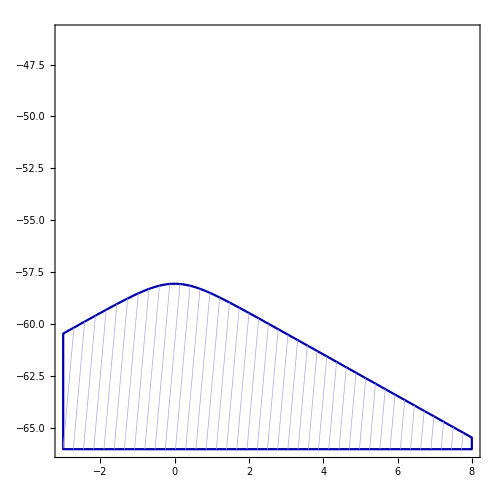

```mathematica
RegionPlot[{ttherm[10^x,10^y,2.1*10^6]≥  tage},{x,-3,8},{y,-46,-66},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Blue],PlotStyle->Directive[Transparent],MeshFunctions->{20*#1-#2&},Mesh->40,MeshStyle->Directive[RGBColor["#AAA6DF"],Thickness[0.001]],PlotRangePadding->None,ImageSize->500]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data10=Import["contact_DD.dat","Table"];
```

```mathematica
data11=Import["10MeV_DD.dat","Table"];
```

```mathematica
dataxenon=Import["xenon.dat","Table"];
```

```mathematica
data10//Grid
```

0.70202 | -42.1538
1.0303 | -44.7521
1.60606 | -46.0513
2.5303 | -45.3846
4 | -43.9487
6. | -41.9487
8. | -39.9487

```mathematica
data11//Grid
```

0.70202 | -40.9402
1.19192 | -43.2137
2.05556 | -43.0256
4 | -41.1282
6. | -39.1282
8. | -37.1282

```mathematica
Log10[dataxenon]//Grid//N
```

0.778151 | -43.6038
0.90309 | -44.6882
0.954243 | -45.0269
1. | -45.2684
1.17609 | -45.9318
1.30103 | -46.2472
1.47712 | -46.3925
1.69897 | -46.279
1.8451 | -46.1681
2. | -46.04
2.17609 | -45.8827
2.30103 | -45.7645
2.60206 | -45.4763
3. | -45.0841
4. | -44.0857
6. | -42.0857
8. | -40.0857

```mathematica
(*Show[Plot[-42,{x,1,8},PlotRange->{{1,8},{-46,-57}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},ImageSize->620,FrameTicks->myticks,AspectRatio->1],ListPlot[{Table[{Log10[dataxenon[[i,1]]],Log10[dataxenon[[i,2]]]-4},{i,Length[dataxenon]}]},PlotRange->{{1,8},{-46,-57}},PlotStyle->Directive[RGBColor["#454545"]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,InterpolationOrder->2,Joined->True,Filling->Top,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,FrameTicks->myticks]]*)
```

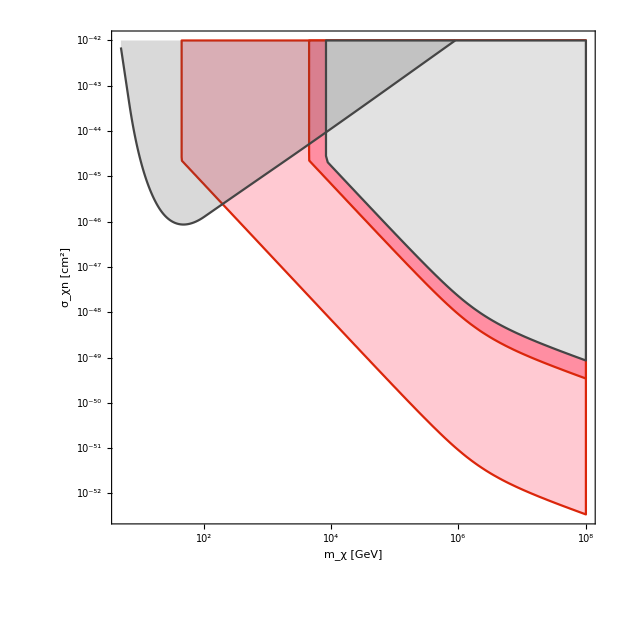

```mathematica
pv3=Show[Plot[-42,{x,1,8},PlotRange->{{1,8},{-46,-57}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},ImageSize->620,FrameTicks->myticks,AspectRatio->1],
RegionPlot[{10^3/0.4*totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,1,8},{y,-46,-57},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FFC9D2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],

RegionPlot[{1/0.4*totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,1,8},{y,-46,-57},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FF8EA2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],

RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,3,8},{y,-46,-58},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},BoundaryStyle->Directive[RGBColor["#454545"]],PlotStyle->Directive[RGBColor["#E2E2E2"]],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],




ListPlot[{Table[{data10[[i,1]],data10[[i,2]]-4},{i,Length[data10]}]},PlotRange->{{1,6},{-46,-57}},PlotStyle->Directive[RGBColor["#454545"]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,Joined->True,Filling->Top,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,InterpolationOrder->2,FrameTicks->myticks]]//Quiet
```

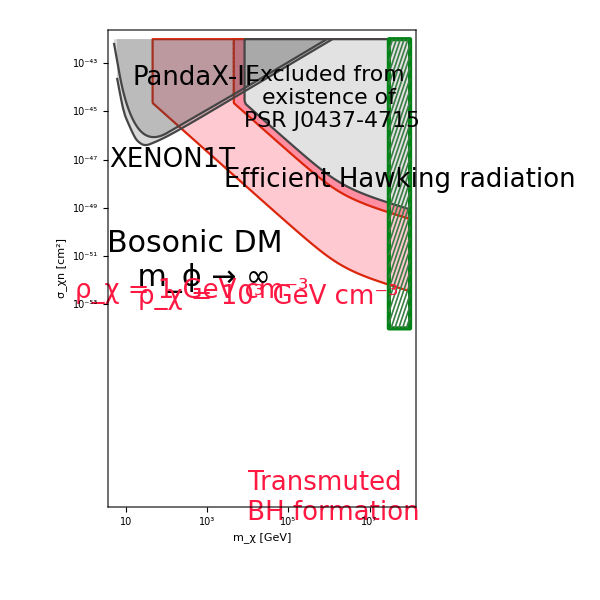

```mathematica
pv3v2=Show[Plot[-42,{x,1,8},PlotRange->{{1,8},{-46,-57}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,ImageSize->600,FrameTicksStyle->38,FrameStyle->Directive[18, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->44],Style["σ_χn [cm^2]",FontSize->44]},FrameTicks->myticks,AspectRatio->1],-Graphics-,ListPlot[{Table[{Log10[dataxenon[[i,1]]],Log10[dataxenon[[i,2]]]-4},{i,Length[dataxenon]}]},PlotRange->{{1,8},{-46,-57}},PlotStyle->Directive[RGBColor["#454545"]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,InterpolationOrder->2,Joined->True,Filling->Top,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,FrameTicks->myticks],
RegionPlot[{10^x≥ 3*10^7},{x,3,8},{y,-46,-58},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],MeshFunctions->{5*#1-#2&},Mesh->30,MeshStyle->Directive[RGBColor["#3A7D44"],Thickness[0.002]],PlotStyle->Directive[Transparent],BoundaryStyle->Directive[RGBColor["#018315"],Thickness[0.005]],PlotRangePadding->None,ImageSize->500],Graphics[Rotate[Text[Style["Efficient Hawking radiation",Darker[Black],FontSize->26],{7.75,-51.83}],90 Degree]],Graphics[Rotate[Text[Style["Excluded from \n existence of \n PSR J0437-4715 ",Darker[Black],FontSize->22],{6.,-48.43}],0 Degree]],Graphics[Rotate[Text[Style["PandaX-II",Darker[Black],FontSize->26],{2.65,-47.63}],0 Degree]],Graphics[Rotate[Text[Style["XENON1T",Darker[Black],FontSize->26],{2.15,-51.0}],0 Degree]],Graphics[Rotate[Text[Style[Framed["Bosonic DM \n m_ϕ → ∞",FrameStyle->Directive[Dashed,Thick]],Darker[Black],FontSize->30],{2.8,-55.2}],0 Degree]],Graphics[Text[Style["ρ_χ = 10^3 GeV cm^-3",RGBColor["#FF1841"],FontSize->26],Scaled[{0.52,0.44}],Scaled[{0.6,0.7}],{0.8,-0.8}]],Graphics[Text[Style["ρ_χ = 1 GeV cm^-3",RGBColor["#FF1841"],FontSize->26],Scaled[{0.65,0.48}],Scaled[{0.8,0.85}],{0.8,-0.8}]],Graphics[Rotate[Text[Style["Transmuted \n BH formation",RGBColor["#FF1841"],FontSize->26],{6.,-65.03}],0 Degree]]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Export["TBH_NS_Boson.pdf",pv3];*)
Export["TBH_NS_Boson.pdf",pv3v2];
```

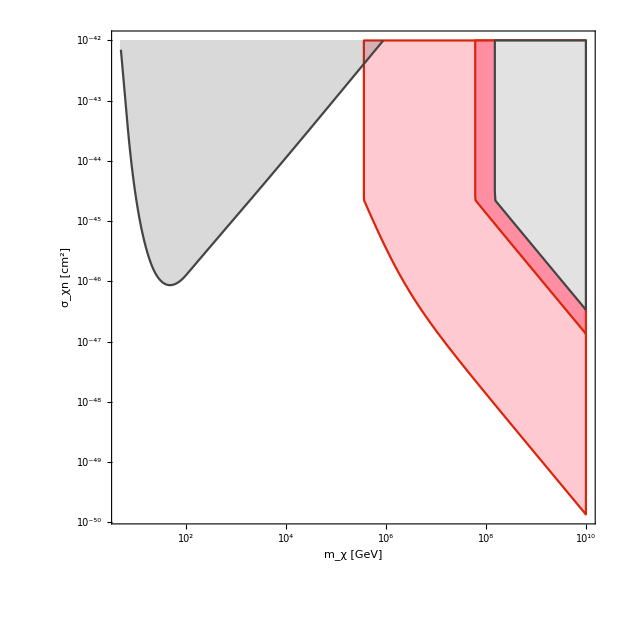

```mathematica
pv4=Show[Plot[-42,{x,5,10},PlotRange->{{5,10},{-46,-55}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},ImageSize->620,FrameTicks->myticks,AspectRatio->1],
RegionPlot[{10^3/0.4*totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchFermion[10^x]]},{x,5,10},{y,-46,-57},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FFC9D2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],

RegionPlot[{1/0.4*totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchFermion[10^x]]},{x,5,10},{y,-46,-57},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FF8EA2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],


RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchFermion[10^x]]},{x,5,10},{y,-46,-58},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},BoundaryStyle->Directive[RGBColor["#454545"]],PlotStyle->Directive[RGBColor["#E2E2E2"]],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],

ListPlot[{Table[{data10[[i,1]],data10[[i,2]]-4},{i,Length[data10]}]},PlotRange->{{1,6},{-46,-57}},PlotStyle->Directive[RGBColor["#454545"]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,Joined->True,Filling->Top,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,InterpolationOrder->2,FrameTicks->myticks]]//Quiet
```

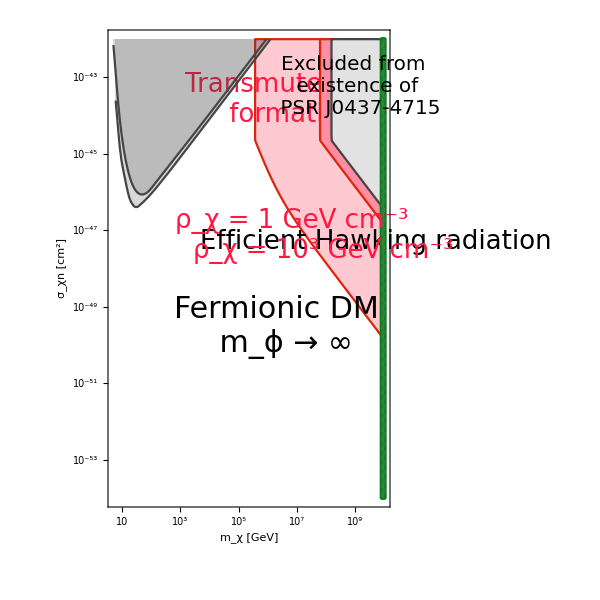

```mathematica
pv4v2=Show[Plot[-42,{x,5,10},PlotRange->{{5,10},{-46,-55}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameTicksStyle->38,FrameStyle->Directive[18, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->44],Style["σ_χn [cm^2]",FontSize->44]},ImageSize->600,FrameTicks->myticks,AspectRatio->1],-Graphics-,ListPlot[{Table[{Log10[dataxenon[[i,1]]],Log10[dataxenon[[i,2]]]-4},{i,Length[dataxenon]}]},PlotRange->{{1,8},{-46,-57}},PlotStyle->Directive[RGBColor["#454545"]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,InterpolationOrder->2,Joined->True,Filling->Top,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,FrameTicks->myticks],RegionPlot[{10^x≥ 8*10^9},{x,5,10},{y,-46,-58},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],MeshFunctions->{5*#1-#2&},Mesh->50,MeshStyle->Directive[RGBColor["#3A7D44"],Thickness[0.002]],PlotStyle->Directive[Transparent],BoundaryStyle->Directive[RGBColor["#018315"],Thickness[0.005]],PlotRangePadding->None,ImageSize->500],  Graphics[Rotate[Text[Style["Efficient Hawking radiation",Darker[Black],FontSize->26],{9.7,-51.3}],90 Degree]],Graphics[Text[Style["ρ_χ = 10^3 GeV cm^-3",RGBColor["#FF1841"],FontSize->26],Scaled[{0.3,0.51}],Scaled[{-0.25,-0.15}],{0.9,-0.48}]],Graphics[Text[Style["ρ_χ = 1 GeV cm^-3",RGBColor["#FF1841"],FontSize->26],Scaled[{0.65,0.6}],Scaled[{0.3,0.5}],{0.4,-0.22}]],
Graphics[Rotate[Text[Style[Framed["Fermionic DM \n m_ϕ → ∞",FrameStyle->Directive[Dashed,Thick]],Darker[Black],FontSize->30],{6.45,-53.53}],0 Degree]],Graphics[Rotate[Text[Style["Excluded from \n existence of \n PSR J0437-4715 ",Darker[Black],FontSize->20],{9.05,-47.23}],0 Degree]],Graphics[Rotate[Text[Style["Transmuted BH \n formation",RGBColor["#FF1841"],FontSize->26],{6.7,-47.6}],0 Degree]]]
```

```mathematica
(*Export["TBH_NS_Fermion.pdf",pv4];*)
Export["TBH_NS_Fermion.pdf",pv4v2];
```

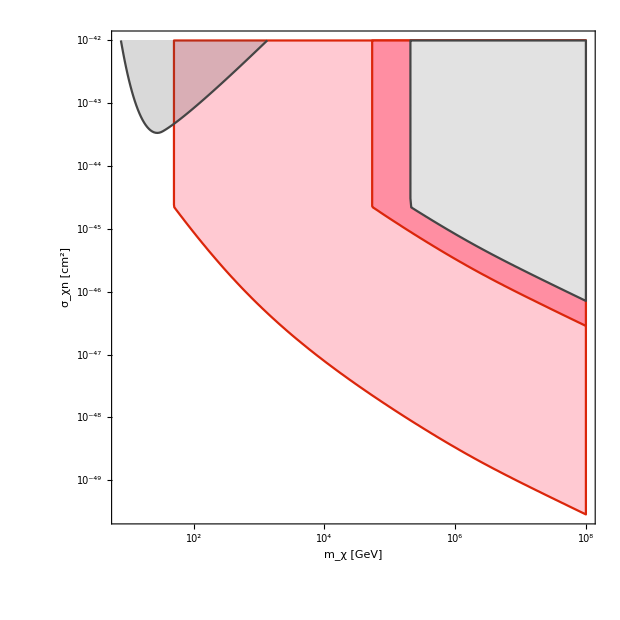

```mathematica
pv5=Show[Plot[-42,{x,1,8},PlotRange->{{1,8},{-46,-54}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},ImageSize->620,FrameTicks->myticks,AspectRatio->1],
RegionPlot[{10^3/0.4*totcapgen[10^x,10^y,0.01]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,1,8},{y,-46,-57},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FFC9D2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],

RegionPlot[{1/0.4*totcapgen[10^x,10^y,0.01]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,1,8},{y,-46,-57},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FF8EA2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],


RegionPlot[{totcapgen[10^x,10^y,0.01]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,3,8},{y,-46,-58},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},BoundaryStyle->Directive[RGBColor["#454545"]],PlotStyle->Directive[RGBColor["#E2E2E2"]],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],

ListPlot[{Table[{data11[[i,1]],data11[[i,2]]-4},{i,Length[data11]}]},PlotRange->{{1,6},{-46,-57}},PlotStyle->Directive[RGBColor["#454545"]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,Joined->True,Filling->Top,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,InterpolationOrder->2,FrameTicks->myticks]]//Quiet
```

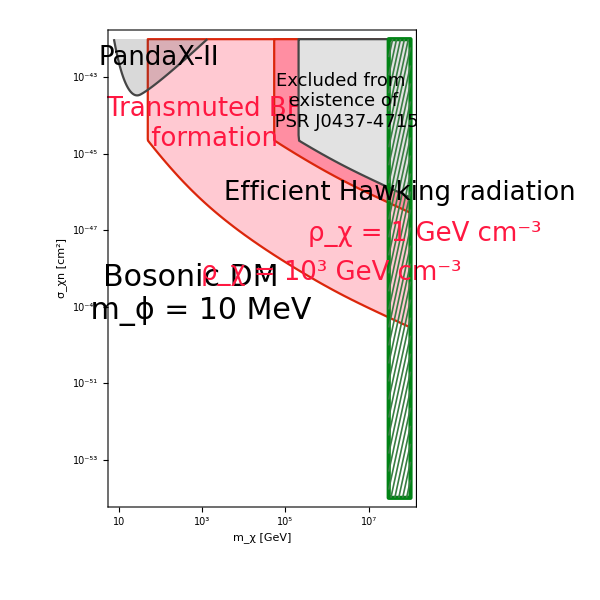

```mathematica
pv5v2=Show[Plot[-42,{x,1,8},PlotRange->{{1,8},{-46,-54}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameTicksStyle->38,FrameStyle->Directive[18, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->44],Style["σ_χn [cm^2]",FontSize->44]},ImageSize->600,FrameTicks->myticks,AspectRatio->1],-Graphics-,RegionPlot[{10^x≥ 3*10^7},{x,3,8},{y,-46,-58},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],MeshFunctions->{5*#1-#2&},Mesh->30,MeshStyle->Directive[RGBColor["#3A7D44"],Thickness[0.002]],PlotStyle->Directive[Transparent],BoundaryStyle->Directive[RGBColor["#018315"],Thickness[0.005]],PlotRangePadding->None,ImageSize->500],

Graphics[Rotate[Text[Style["Efficient Hawking radiation",Darker[Black],FontSize->26],{7.75,-50.03}],90 Degree]],Graphics[Rotate[Text[Style["Excluded from \n existence of \n PSR J0437-4715 ",Darker[Black],FontSize->18],{6.4,-47.63}],0 Degree]],Graphics[Rotate[Text[Style["PandaX-II",Darker[Black],FontSize->26],{1.95,-46.48}],0 Degree]],Graphics[Rotate[Text[Style[Framed["Bosonic DM \n m_ϕ = 10 MeV",FrameStyle->Directive[Dashed,Thick]],Darker[Black],FontSize->30],{2.85,-52.68}],0 Degree]],Graphics[Rotate[Text[Style["Transmuted BH \n formation",RGBColor["#FF1841"],FontSize->26],{3.2,-48.23}],0 Degree]],Graphics[Text[Style["ρ_χ = 10^3 GeV cm^-3",RGBColor["#FF1841"],FontSize->26],Scaled[{0.3,0.49}],Scaled[{-0.35,0.55}],{0.9,-0.48}]],Graphics[Text[Style["ρ_χ = 1 GeV cm^-3",RGBColor["#FF1841"],FontSize->26],Scaled[{0.65,0.6}],Scaled[{0.25,1.}],{0.4,-0.2}]]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Export["TBH_NS_Boson_10_MeV.pdf",pv5];*)
Export["TBH_NS_Boson_10_MeV.pdf",pv5v2];
```

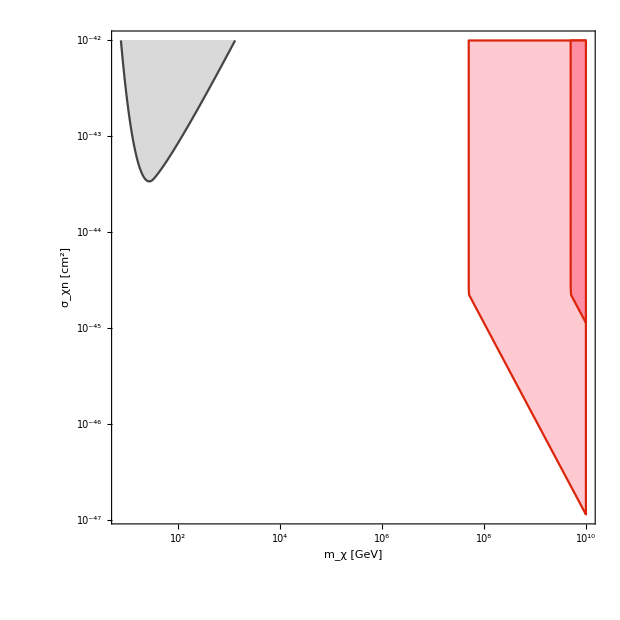

```mathematica
pv6=Show[Plot[-42,{x,5,10},PlotRange->{{7,10},{-46,-51}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},ImageSize->620,FrameTicks->myticks,AspectRatio->1],
RegionPlot[{10^3/0.4*totcapgen[10^x,10^y,0.01]≥Max[ Nself[10^x,2.1*10^6],NchFermion[10^x]]},{x,5,10},{y,-46,-57},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FFC9D2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],

RegionPlot[{10/0.4*totcapgen[10^x,10^y,0.01]≥Max[ Nself[10^x,2.1*10^6],NchFermion[10^x]]},{x,5,10},{y,-46,-57},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FF8EA2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],




ListPlot[{Table[{data11[[i,1]],data11[[i,2]]-4},{i,Length[data11]}]},PlotRange->{{1,6},{-46,-57}},PlotStyle->Directive[RGBColor["#454545"]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,Joined->True,Filling->Top,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,InterpolationOrder->2,FrameTicks->myticks]]//Quiet
```

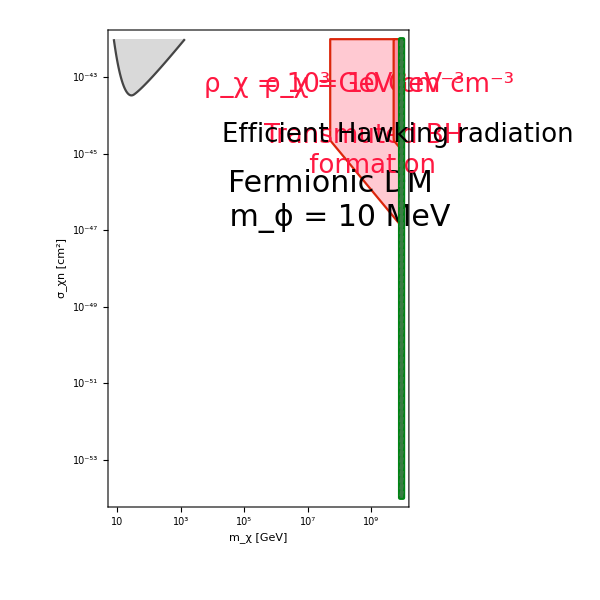

```mathematica
pv6v2=Show[Plot[-42,{x,5,10},PlotRange->{{7,10},{-46,-51}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameTicksStyle->38,FrameStyle->Directive[18, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->44],Style["σ_χn [cm^2]",FontSize->44]},ImageSize->600,FrameTicks->myticks,AspectRatio->1],-Graphics-,RegionPlot[{10^x≥ 8*10^9},{x,5,10},{y,-46,-58},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],MeshFunctions->{5*#1-#2&},Mesh->70,MeshStyle->Directive[RGBColor["#3A7D44"],Thickness[0.002]],PlotStyle->Directive[Transparent],BoundaryStyle->Directive[RGBColor["#018315"],Thickness[0.005]],PlotRangePadding->None,ImageSize->500],Graphics[Rotate[Text[Style["Efficient Hawking radiation",Darker[Black],FontSize->26],{9.82,-48.50}],90 Degree]],Graphics[Rotate[Text[Style[Framed["Fermionic DM \n m_ϕ = 10 MeV",FrameStyle->Directive[Dashed,Thick]],Black,FontSize->30],{7.85,-50.23}],0 Degree]],Graphics[Rotate[Text[Style["ρ_χ = 10^3 GeV cm^-3",RGBColor["#FF1841"],FontSize->26],{7.84,-47.2}],90 Degree]],Graphics[Rotate[Text[Style["ρ_χ = 10 GeV cm^-3",RGBColor["#FF1841"],FontSize->26],{9.57,-47.2}],90 Degree]],Graphics[Rotate[Text[Style["Transmuted BH \n formation",RGBColor["#FF1841"],FontSize->26],{8.9,-48.93}],0 Degree]]]
```

```mathematica
(*Export["TBH_NS_Fermion_10_MeV.pdf",pv6];*)
```

```mathematica
Export["TBH_NS_Fermion_10_MeV.pdf",pv6v2];
```

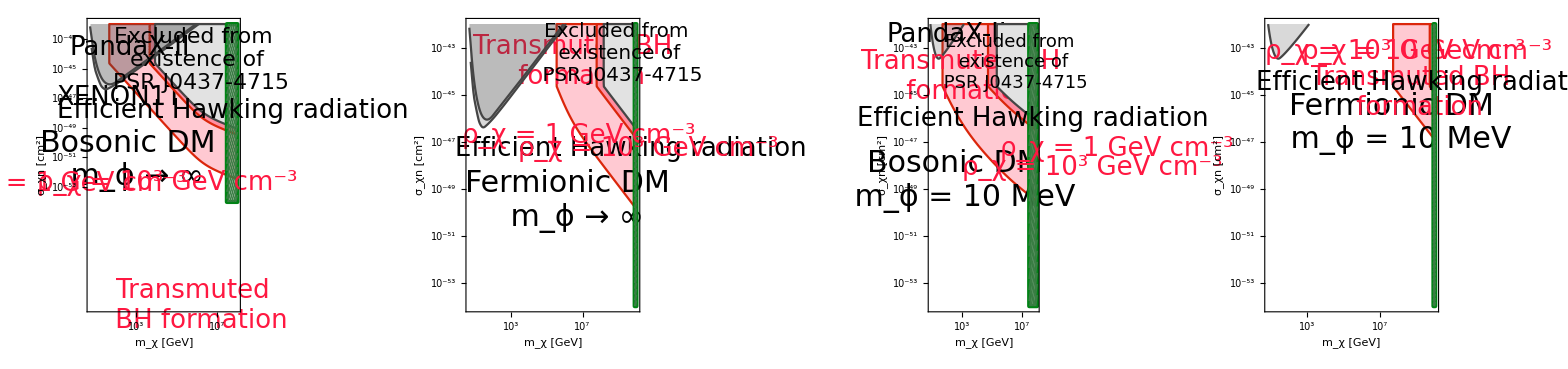

```mathematica
GraphicsRow[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},ImageSize->2800]
```

```mathematica
(*NS-NS merger rate with redshift*)(*Taylor et al.*)
```

```mathematica
τtrans=4.58*10^9;(*in year*)
```

```mathematica
tb[q_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,q,∞}];(*in year*)
```

```mathematica
t[z_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,z,∞}];(*in year*)
```

```mathematica
t[0]
```

1.37967×10^10

```mathematica
tstar=t[10]
```

4.88599×10^8

```mathematica
R2[z_]:=If[z≤ 10,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[z]-tb[q])),{q,z,10}],0](*in Mpc^-3 yr^-1*)//Quiet(*SFR is adapated from Vattis et. al.*)
```

```mathematica
R2[0.001]
```

6.35338×10^-6

```mathematica
p1=Table[{z,R2[z]},{z,0.1,1.2,0.1}];
```

```mathematica
p2=Table[{z,R2[z]},{z,1.4,1.7,0.1}];
```

```mathematica
p3=Table[{z,R2[z]},{z,1.9,9.9,1}];
```

```mathematica
q=Join[{{0.001,6.35338*10^-6}},p1,p2,p3]
```

{{0.001,6.35338×10^-6},{0.1,7.56561×10^-6},{0.2,9.96882×10^-6},{0.3,0.0000119608},{0.4,0.0000148564},{0.5,0.0000173709},{0.6,0.0000197247},{0.7,0.0000230037},{0.8,0.0000246815},{0.9,0.0000294361},{1.,0.00003051},{1.1,0.0000344488},{1.2,0.0000387909},{1.4,0.0000439225},{1.5,0.0000457582},{1.6,0.0000484401},{1.7,0.0000493154},{1.9,0.000048892},{2.9,0.0000330092},{3.9,0.0000191909},{4.9,0.0000113842},{5.9,7.23368×10^-6},{6.9,5.13988×10^-6},{7.9,3.67582×10^-6},{8.9,2.53744×10^-6},{9.9,1.84956×10^-6}}

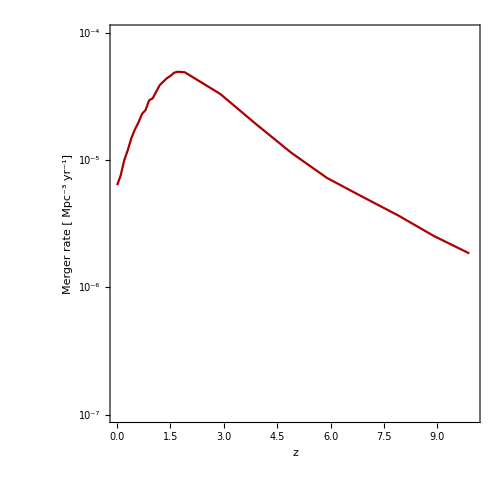

```mathematica
ListLogPlot[{Table[{q[[i,1]],q[[i,2]]},{i,1,Length[q]}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10^-4,10^-7}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [ Mpc^-3 yr^-1]",FontSize->20]},PlotStyle->Darker[Red]]
```

```mathematica
f[z_]:=t[z]-τtrans;(*in year*)
```

```mathematica
f[0]
```

9.21666×10^9

```mathematica
FindRoot[t[z]==f[0],{z,10}]//Quiet
```

{z→0.435569}

```mathematica
f[0.1]
```

7.91903×10^9

```mathematica
FindRoot[t[z]==f[0.1],{z,10}]//Quiet
```

{z→0.620772}

```mathematica
f[0.2]
```

6.78641×10^9

```mathematica
FindRoot[t[z]==f[0.2],{z,10}]//Quiet
```

{z→0.824073}

```mathematica
f[0.3]
```

5.79399×10^9

```mathematica
FindRoot[t[z]==f[0.3],{z,10}]//Quiet
```

{z→1.05035}

```mathematica
f[0.4]
```

4.92142×10^9

```mathematica
FindRoot[t[z]==f[0.4],{z,10}]//Quiet
```

{z→1.30601}

```mathematica
f[0.5]
```

4.15172×10^9

```mathematica
FindRoot[t[z]==f[0.5],{z,10}]//Quiet
```

{z→1.59977}

```mathematica
f[0.6]
```

3.47056×10^9

```mathematica
FindRoot[t[z]==f[0.6],{z,10}]//Quiet
```

{z→1.94397}

```mathematica
f[0.7]
```

2.86583×10^9

```mathematica
FindRoot[t[z]==f[0.7],{z,10}]//Quiet
```

{z→2.35683}

```mathematica
f[0.8]
```

2.32721×10^9

```mathematica
FindRoot[t[z]==f[0.8],{z,10}]//Quiet
```

{z→2.86679}

```mathematica
f[0.9]
```

1.84591×10^9

```mathematica
FindRoot[t[z]==f[0.9],{z,10}]//Quiet
```

{z→3.52122}

```mathematica
f[1.0]
```

1.41443×10^9

```mathematica
FindRoot[t[z]==f[1.0],{z,10}]//Quiet
```

{z→4.40651}

```mathematica
f[1.1]
```

1.02639×10^9

```mathematica
FindRoot[t[z]==f[1.1],{z,10}]//Quiet
```

{z→5.70119}

```mathematica
f[1.2]
```

6.76306×10^8

```mathematica
FindRoot[t[z]==f[1.2],{z,10}]//Quiet
```

{z→7.85474}

```mathematica
f[1.3](*t[1.3]-τtrans is less than tstar=4.88599*10^8 year, hence mereger rate is zero*)
```

3.59492×10^8

```mathematica
R2trans={{0,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0]-tb[q])),{q,0.435569,10}]},{0.1,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0.1]-tb[q])),{q,0.620772,10}]},{0.2,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0.2]-tb[q])),{q,0.824073,10}]},{0.3,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0.3]-tb[q])),{q,1.05035,10}]},{0.4,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0.4]-tb[q])),{q,1.30601,10}]},{0.5,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0.5]-tb[q])),{q,1.59977,10}]},{0.6,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0.6]-tb[q])),{q,1.94397,10}]},{0.7,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0.7]-tb[q])),{q,2.35683,10}]},{0.8,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0.8]-tb[q])),{q,2.86679,10}]},{0.9,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[0.9]-tb[q])),{q,3.52122,10}]},{1.0,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[1.0]-tb[q])),{q,4.40651,10}]},{1.1,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[1.1]-tb[q])),{q,5.70119,10}]},{1.2,NIntegrate[((0.015*10^-5)/(70.4*1/(3.086*10^19)*3.154*10^7)*(1+q)^1.7/(1+((1+q)/2.9)^5.6)*1/((0.73+0.27*(1+q)^3)^0.5)*1/(t[1.2]-tb[q])),{q,6.76306,10}]}}//Quiet
```

{{0,8.17025×10^-7},{0.1,8.27517×10^-7},{0.2,8.07615×10^-7},{0.3,7.52227×10^-7},{0.4,6.6008×10^-7},{0.5,5.37225×10^-7},{0.6,3.99253×10^-7},{0.7,2.67916×10^-7},{0.8,1.61408×10^-7},{0.9,8.66667×10^-8},{1.,4.04281×10^-8},{1.1,1.51029×10^-8},{1.2,7.34121×10^-9}}

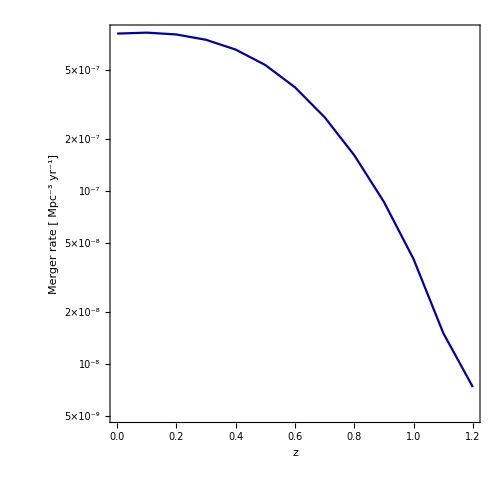

```mathematica
ListLogPlot[{Table[{R2trans[[i,1]],R2trans[[i,2]]},{i,1,Length[R2trans]}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [ Mpc^-3 yr^-1]",FontSize->20]},PlotStyle->Darker[Blue]]
```

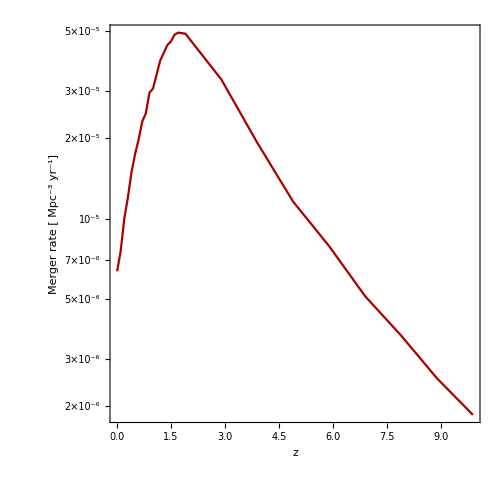
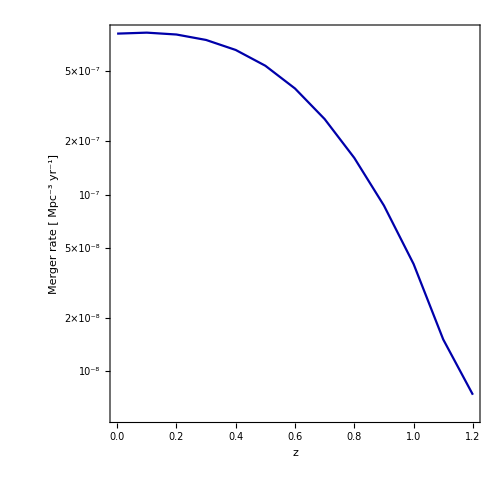
```mathematica
Show[-Graphics-,-Graphics-]
```

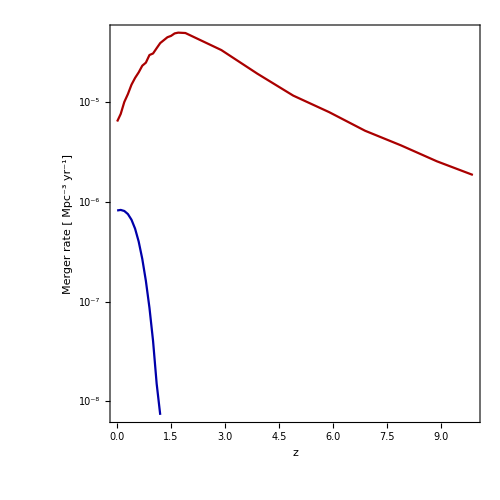

```mathematica
(*NS-NS merger rate with redshift*)(*Taylor et al.*)(*1.3 Solar mass Neutron Star*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*);(*scaled for a general ρ later*)
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
tage=6.69*10^9*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27);
Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
NchFermion[mx_?NumericQ]:=Mpl^3/mx^3;
```

```mathematica
GN=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
cns=0.17;
λ=0.25;
```

```mathematica
mcrit=1/GN*(cns^3/(74*π*4*π*λ*ρ*5.62*10^26*(1.98*10^-16)^3))^0.25;(*critical mass for BH evaporation in GeV*)
```

```mathematica
mcrit
```

2.71619×10^37

```mathematica
τcollapse[mx_?NumericQ,T_?NumericQ]:=cns^3/(4*π*λ*ρ*10^-3*5.62*10^23*(1.98*10^-14)^3*GN^2*mx*Max[Nself[mx,T],NchBoson[mx]])*6.58*10^-25*1/(3.15*10^7);(*in year, time required to consume the host star*)
```

```mathematica
τtrans[ρ_?NumericQ,mx_?NumericQ,T_?NumericQ,sigma_?NumericQ]:=1/(ρ/0.4*auni[mx,sigma])*Max[Nself[mx,T],NchBoson[mx]]*1/(3.15*10^7)+τcollapse[mx,T];
(*in year, time required to transmute, first term presents time required to capture enough DM particles to achieve the BH foramtion criterion, second term presents time required to consume the host star*)
```

```mathematica
τtrans[1000,10^4,2.1*10^6,10^-49]
```

4.57861×10^6

```mathematica
tage*1/(3.15*10^7)//N
```

6.69×10^9

```mathematica
Max[Nself[10^4,2.1*10^6],NchBoson[10^4]]
```

4.59708×10^38

```mathematica
1000/0.4*totcapuni[10^4,10^-49]
```

6.71702×10^41

```mathematica
t[z_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,z,∞}];(*in year*)
```

```mathematica
tstar=t[10]
```

4.88599×10^8

```mathematica
f[zb_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,zb,∞}];
```

```mathematica
p1=Table[{i*10^9,zb/.FindRoot[f[zb]==i*10^9,{zb,0}]},{i,0.01,13.79,0.01}];//Quiet
```

```mathematica
f1=Interpolation[Table[{p1[[i,1]],p1[[i,2]]},{i,1,Length[p1]}]];
```

```mathematica
mergerns[z_]:=If[tstar≤ t[z],NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,t[z]}],0]//Quiet(*normalization is added following Taylor et al.*)
```

```mathematica
ρc[z_]=1.05*10^-5*0.704^2*(0.73+0.27*(1+z));(*in GeV/cm^3*)
```

```mathematica
c200=13.31;

m200=0.82*10^12*2*10^33*5.62*10^23;(*in GeV*)
```

```mathematica
rs[z_]:=(m200/(4/3*π*c200^3*200*ρc[z]))^(1/3)*1/(3.086*10^21);(*in kpc*)
```

```mathematica
rs[0]
```

14.5034

```mathematica
ρs[z_]:=m200/(4*π*rs[z]^3*(3.086*10^21)^3*(Log[1+c200]-c200/(1+c200)));(*in GeV/cm^3*)
```

```mathematica
ρs[0]
```

0.472629

```mathematica
ρNFW[r_,z_]:=ρs[z]/(r/rs[z]*(1+r/rs[z])^2);(*DM density at GeV/cm^3 for NFW profile at various redshifts*)
```

```mathematica
ρNFW[8.5,0]
```

0.320571

```mathematica
mergertrans1[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.01,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.015,z],mx,T,sigma])}],0];(*merger rate assuming the NS are at 0.01-0.02 kpc*)(*in Mpc^-3 yr^-1*)
```

```mathematica
mergertrans2[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.02,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.025,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans3[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.03,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.035,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans4[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.04,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.045,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans5[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.05,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.055,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans6[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.06,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.065,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans7[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.07,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.075,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans8[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.08,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.085,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans9[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.09,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.095,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans[mx_,T_,sigma_,z_]:=1/9*(mergertrans1[mx,T,sigma,z]+mergertrans2[mx,T,sigma,z]+mergertrans3[mx,T,sigma,z]+mergertrans4[mx,T,sigma,z]+mergertrans5[mx,T,sigma,z]+mergertrans6[mx,T,sigma,z]+mergertrans7[mx,T,sigma,z]+mergertrans8[mx,T,sigma,z]+mergertrans9[mx,T,sigma,z]);
```

```mathematica
((1.3*1.3)^(3/5)/(1.3+1.3)^(1/5))^(6/5)
```

1.16007

```mathematica
mergertrans[10^4,2.1*10^6,10^-49,0]*10^9
```

308.94

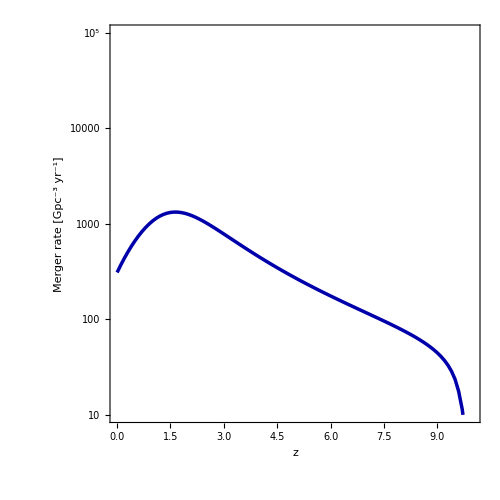

```mathematica
ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-49,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Blue],Thickness[0.005]]]
```

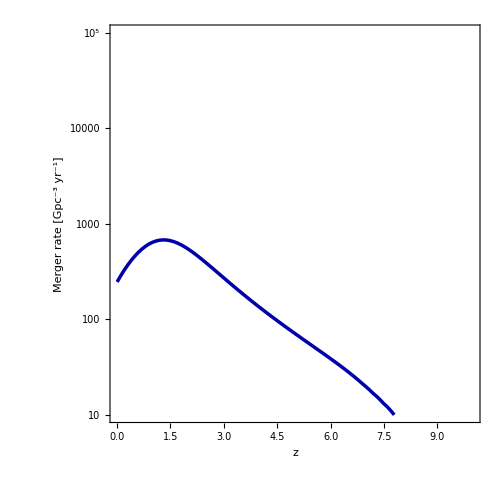

```mathematica
ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-50,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Blue],Thickness[0.005]]]
```

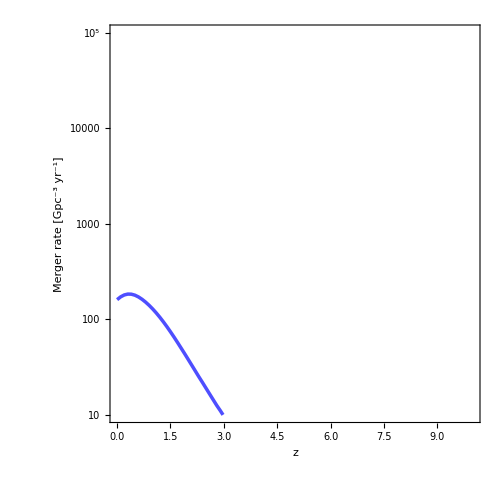

```mathematica
ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-51,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[RGBColor["#4E4EFF"],Thickness[0.005]]]
```

```mathematica
q=Join[Table[{z,10^9*mergerns[z]},{z,0,2,0.2}],Table[{z,10^9*mergerns[z]},{z,2,9,0.5}],{{9.9,10^9*mergerns[9.9]}}];
```

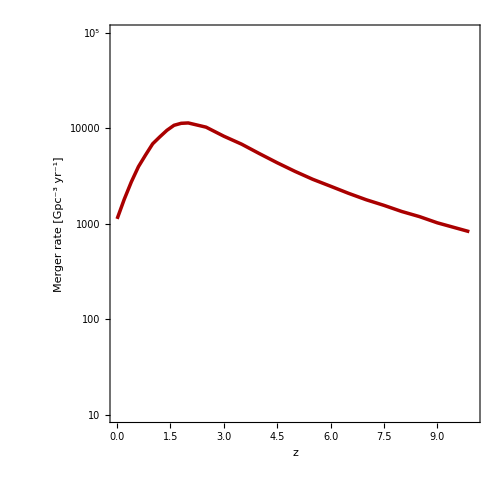

```mathematica
ListLogPlot[{Table[{q[[i,1]],q[[i,2]]},{i,1,Length[q]}]},Frame->True,Joined->True,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Red],Thickness[0.005]],PlotRangePadding->None]
```

```mathematica
t[z_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,z,∞}];(*in year*)
```

```mathematica
R[fpbh_,mpbh_,z_]:=1.6*10^6*(fpbh)^(53/37)*(1/4)^(-34/37)*2^(-32/37)*mpbh^(-32/37)*(t[z]/t[0])^(-34/37)*((5*0.01^2)/(6*0.007))^(21/74)*HypergeometricU[21/74,1/2,(5*0.01^2)/(6*0.007)];(*in Gpc^-3 yr^-1*)(*see 1812.01930, 1801.10327*)
```

```mathematica
myticks={{{{10,"10"},{20,""},{30,""},{40,""},{50,""},{60,""},{70,""},{80,""},{90,""},{100,"10^2",{0.015,0}},{200,""},{300,""},{400,""},{500,""},{600,""},{700,""},{800,""},{900,""},{1000,"10^3",{0.015,0}},{2000,""},{3000,""},{4000,""},{5000,""},{6000,""},{7000,""},{8000,""},{9000,""},{10^4,"10^4",{0.015,0}},{20000,""},{30000,""},{40000,""},{50000,""},{60000,""},{70000,""},{80000,""},{90000,""},{10^5,"10^5",{0.015,0}},{2*10^5,""},{3*10^5,""},{4*10^5,""},{5*10^5,""},{6*10^5,""},{7*10^5,""},{8*10^5,""},{9*10^5,""},{10^6,"10^6",{0.015,0}}}, {{10,""},{20,""},{30,""},{40,""},{50,""},{60,""},{70,""},{80,""},{90,""},{100,"",{0.015,0}},{200,""},{300,""},{400,""},{500,""},{600,""},{700,""},{800,""},{900,""},{1000,"",{0.015,0}},{2000,""},{3000,""},{4000,""},{5000,""},{6000,""},{7000,""},{8000,""},{9000,""},{10^4,"",{0.015,0}},{20000,""},{30000,""},{40000,""},{50000,""},{60000,""},{70000,""},{80000,""},{90000,""},{10^5,"",{0.015,0}},{2*10^5,""},{3*10^5,""},{4*10^5,""},{5*10^5,""},{6*10^5,""},{7*10^5,""},{8*10^5,""},{9*10^5,""},{10^6,"",{0.015,0}}}},{Automatic,Automatic}};
```

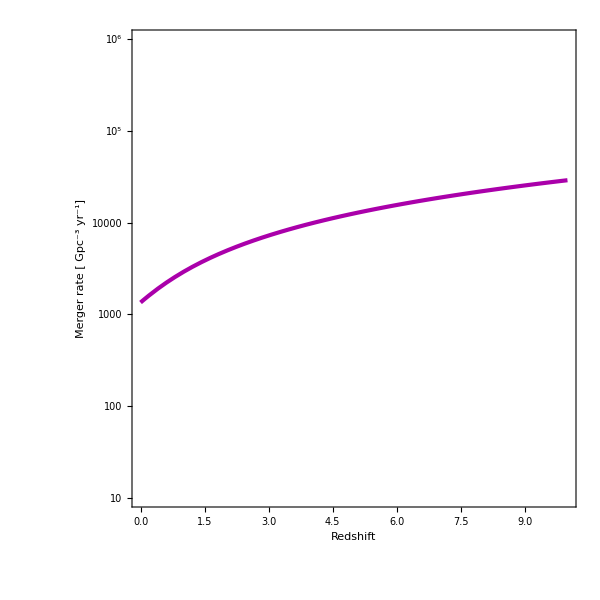

```mathematica
LogPlot[R[0.01,1.3,z],{z,0,10},Frame->True,AspectRatio->1,ImageSize->600,FrameStyle->Directive[18, "Times",Black,Thickness[0.003]],FrameTicksStyle->24,PlotRange->{{0,10},{10,10^6}},FrameTicks->myticks,FrameLabel->{Style["Redshift",FontSize->28],Style["Merger rate [ Gpc^-3 yr^-1]",FontSize->28]},PlotStyle->Directive[Darker[Magenta],Thickness[0.005]]]
```

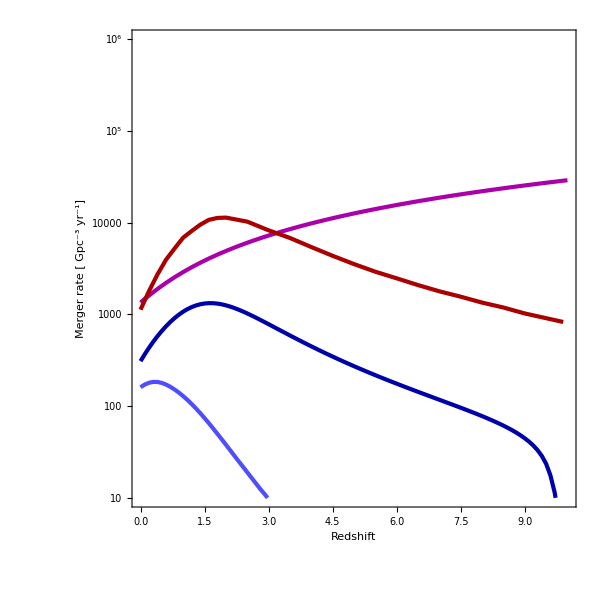

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,Graphics[Rotate[Text[Style["PBH-PBH merger",Darker[Magenta],FontSize->18],Scaled[{0.78,0.72}]],0 Degree]],Graphics[Rotate[Text[Style["NS-NS merger",Darker[Red],FontSize->18],Scaled[{0.84,0.48}]],0 Degree]],Graphics[Rotate[Text[Style["TBH-TBH merger",Darker[Blue],FontSize->18],Scaled[{0.75,0.27}]],0 Degree]],Graphics[Rotate[Text[Style["TBH-TBH merger",RGBColor["#4E4EFF"],FontSize->18],Scaled[{0.42,0.07}]],0 Degree]],Graphics[Rotate[Text[Style[" m_χ = 10^4 GeV ",Darker[Blue],FontSize->18],Scaled[{0.52,0.42}]],0 Degree]],Graphics[Rotate[Text[Style[" σ_χn = 10^-45 cm^2 ",Darker[Blue],FontSize->18],Scaled[{0.53,0.37}]],0 Degree]],Graphics[Rotate[Text[Style[" m_χ = 10^4 GeV ",RGBColor["#4E4EFF"],FontSize->18],Scaled[{0.32,0.22}]],0 Degree]],Graphics[Rotate[Text[Style[" σ_χn = 10^-47 cm^2 ",RGBColor["#4E4EFF"],FontSize->18],Scaled[{0.33,0.17}]],0 Degree]]]
```

```mathematica
dh=(3*10^8)/(70.4*1/(3.086*10^19))*3.24*10^-23;(*in Mpc*)
```

```mathematica
dc[z_]:=dh*NIntegrate[1/((0.73+0.27*(1+p)^3)^0.5),{p,0,z}];(*in Mpc*)
```

```mathematica
dL[z_]:=(1+z)*dc[z];
```

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,0.1}]//Quiet
```

2.79608

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,0.1}]//Quiet
```

1.40798

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2}]//Quiet
```

23882.6

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2}]//Quiet
```

5393.63

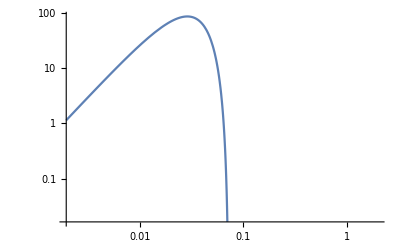

```mathematica
LogLogPlot[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2}]
```

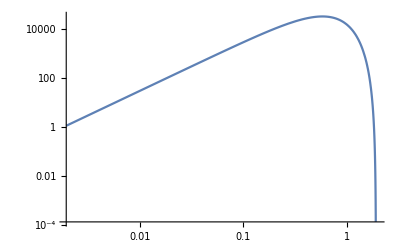

```mathematica
LogLogPlot[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2}]
```

```mathematica
(*NS-NS merger rate with redshift*)(*Taylor et al.*)(*1.0 Solar mass Neutron Star*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.6*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
tage=6.69*10^9*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27);
Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
NchFermion[mx_?NumericQ]:=Mpl^3/mx^3;
```

```mathematica
GN=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
cns=0.17;
λ=0.25;
```

```mathematica
mcrit=1/GN*(cns^3/(74*π*4*π*λ*ρ*5.62*10^26*(1.98*10^-16)^3))^0.25;(*critical mass for BH evaporation in GeV*)
```

```mathematica
mcrit
```

2.71619×10^37

```mathematica
τcollapse[mx_?NumericQ,T_?NumericQ]:=cns^3/(4*π*λ*ρ*10^-3*5.62*10^23*(1.98*10^-14)^3*GN^2*mx*Max[Nself[mx,T],NchBoson[mx]])*6.58*10^-25*1/(3.15*10^7);(*in year, time required to consume the host star*)
```

```mathematica
τtrans[ρ_?NumericQ,mx_?NumericQ,T_?NumericQ,sigma_?NumericQ]:=1/(ρ/0.4*auni[mx,sigma])*Max[Nself[mx,T],NchBoson[mx]]*1/(3.15*10^7)+τcollapse[mx,T];
(*in year, time required to transmute, first term presents time required to capture enough DM particles to achieve the BH foramtion criterion, second term presents time required to consume the host star*)
```

```mathematica
τtrans[1000,10^4,2.1*10^6,10^-49]
```

5.79864×10^6

```mathematica
tage*1/(3.15*10^7)//N
```

6.69×10^9

```mathematica
Max[Nself[10^4,2.1*10^6],NchBoson[10^4]]
```

4.59708×10^38

```mathematica
1000/0.4*totcapuni[10^4,10^-49]
```

5.30376×10^41

```mathematica
t[z_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,z,∞}];(*in year*)
```

```mathematica
tstar=t[10]
```

4.88599×10^8

```mathematica
f[zb_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,zb,∞}];
```

```mathematica
p1=Table[{i*10^9,zb/.FindRoot[f[zb]==i*10^9,{zb,0}]},{i,0.01,13.79,0.01}];//Quiet
```

```mathematica
f1=Interpolation[Table[{p1[[i,1]],p1[[i,2]]},{i,1,Length[p1]}]];
```

```mathematica
mergerns[z_]:=If[tstar≤ t[z],NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,t[z]}],0]//Quiet
```

```mathematica
ρc[z_]=1.05*10^-5*0.704^2*(0.73+0.27*(1+z));(*in GeV/cm^3*)
```

```mathematica
c200=13.31;

m200=0.82*10^12*2*10^33*5.62*10^23;(*in GeV*)
```

```mathematica
rs[z_]:=(m200/(4/3*π*c200^3*200*ρc[z]))^(1/3)*1/(3.086*10^21);(*in kpc*)
```

```mathematica
rs[0]
```

14.5034

```mathematica
ρs[z_]:=m200/(4*π*rs[z]^3*(3.086*10^21)^3*(Log[1+c200]-c200/(1+c200)));(*in GeV/cm^3*)
```

```mathematica
ρNFW[r_,z_]:=ρs[z]/(r/rs[z]*(1+r/rs[z])^2);(*DM density at GeV/cm^3 for NFW profile at various redshifts*)
```

```mathematica
ρNFW[8.5,0]
```

0.320571

```mathematica
mergertrans1[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.01,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.015,z],mx,T,sigma])}],0];(*merger rate assuming the NS are at 0.01-0.02 kpc*)(*in Mpc^-3 yr^-1*)
```

```mathematica
mergertrans2[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.02,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.025,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans3[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.03,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.035,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans4[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.04,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.045,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans5[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.05,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.055,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans6[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.06,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.065,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans7[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.07,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.075,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans8[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.08,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.085,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans9[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.09,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.095,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans[mx_,T_,sigma_,z_]:=1/9*(mergertrans1[mx,T,sigma,z]+mergertrans2[mx,T,sigma,z]+mergertrans3[mx,T,sigma,z]+mergertrans4[mx,T,sigma,z]+mergertrans5[mx,T,sigma,z]+mergertrans6[mx,T,sigma,z]+mergertrans7[mx,T,sigma,z]+mergertrans8[mx,T,sigma,z]+mergertrans9[mx,T,sigma,z]);
```

```mathematica
((1.0*1.0)^(3/5)/(1.0+1.0)^(1/5))^(6/5)
```

0.846745

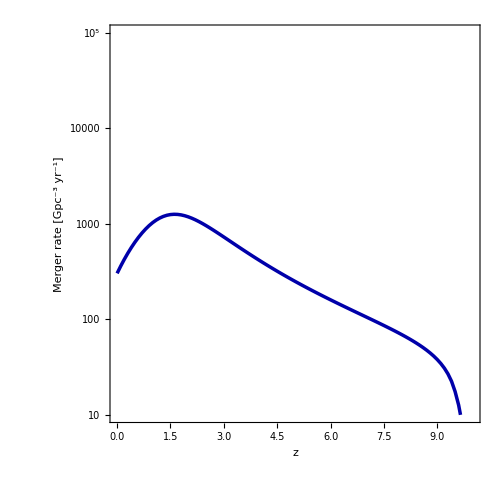

```mathematica
ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-49,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Blue],Thickness[0.005]]]
```

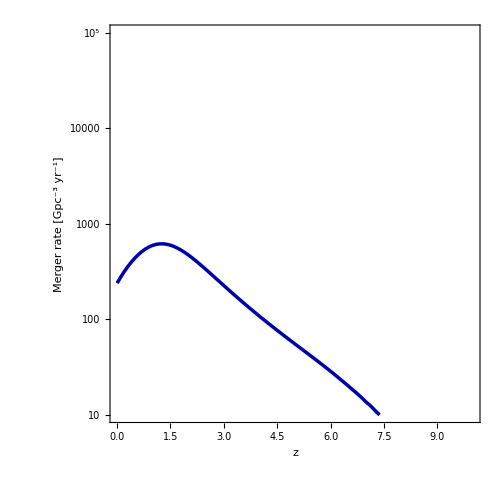

```mathematica
ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-50,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Blue],Thickness[0.005]]]
```

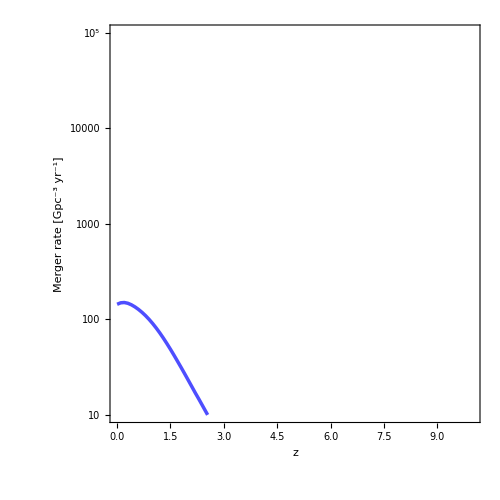

```mathematica
ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-51,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[RGBColor["#4E4EFF"],Thickness[0.005]]]
```

```mathematica
q=Join[Table[{z,10^9*mergerns[z]},{z,0,2,0.2}],Table[{z,10^9*mergerns[z]},{z,2,9,0.5}],{{9.9,10^9*mergerns[9.9]}}];
```

```mathematica
ListLogPlot[{Table[{q[[i,1]],q[[i,2]]},{i,1,Length[q]}]},Frame->True,Joined->True,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Red],Thickness[0.005]],PlotRangePadding->None]
```

-Graphics-

```mathematica
dh=(3*10^8)/(70.4*1/(3.086*10^19))*3.24*10^-23;(*in Mpc*)
```

```mathematica
dc[z_]:=dh*NIntegrate[1/((0.73+0.27*(1+p)^3)^0.5),{p,0,z}];(*in Mpc*)
```

```mathematica
dL[z_]:=(1+z)*dc[z];
```

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,0.1}]//Quiet
```

1.25669

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,0.1}]//Quiet
```

0.578199

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2}]//Quiet
```

10592.7

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2}]//Quiet
```

2371.37

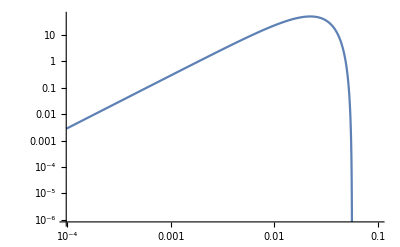

```mathematica
LogLogPlot[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,0.1}]
```

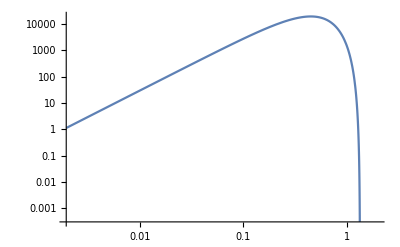

```mathematica
LogLogPlot[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2}]
```

```mathematica
(*Normalized to LIGO-VIRGO*)
```

```mathematica
(*NS-NS merger rate with redshift*)(*Taylor et al.*)(*1.3 Solar mass Neutron Star*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*);(*scaled for a general ρ later*)
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
tage=6.69*10^9*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27);
Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
NchFermion[mx_?NumericQ]:=Mpl^3/mx^3;
```

```mathematica
GN=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
cns=0.17;
λ=0.25;
```

```mathematica
mcrit=1/GN*(cns^3/(74*π*4*π*λ*ρ*5.62*10^26*(1.98*10^-16)^3))^0.25;(*critical mass for BH evaporation in GeV*)
```

```mathematica
mcrit
```

2.71619×10^37

```mathematica
τcollapse[mx_?NumericQ,T_?NumericQ]:=cns^3/(4*π*λ*ρ*10^-3*5.62*10^23*(1.98*10^-14)^3*GN^2*mx*Max[Nself[mx,T],NchBoson[mx]])*6.58*10^-25*1/(3.15*10^7);(*in year, time required to consume the host star*)
```

```mathematica
τtrans[ρ_?NumericQ,mx_?NumericQ,T_?NumericQ,sigma_?NumericQ]:=1/(ρ/0.4*auni[mx,sigma])*Max[Nself[mx,T],NchBoson[mx]]*1/(3.15*10^7)+τcollapse[mx,T];
(*in year, time required to transmute, first term presents time required to capture enough DM particles to achieve the BH foramtion criterion, second term presents time required to consume the host star*)
```

```mathematica
τtrans[1000,10^4,2.1*10^6,10^-49]
```

4.57861×10^6

```mathematica
tage*1/(3.15*10^7)//N
```

6.69×10^9

```mathematica
Max[Nself[10^4,2.1*10^6],NchBoson[10^4]]
```

4.59708×10^38

```mathematica
1000/0.4*totcapuni[10^4,10^-49]
```

6.71702×10^41

```mathematica
t[z_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,z,∞}];(*in year*)
```

```mathematica
tstar=t[10]
```

4.88599×10^8

```mathematica
f[zb_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,zb,∞}];
```

```mathematica
p1=Table[{i*10^9,zb/.FindRoot[f[zb]==i*10^9,{zb,0}]},{i,0.01,13.79,0.01}];//Quiet
```

```mathematica
f1=Interpolation[Table[{p1[[i,1]],p1[[i,2]]},{i,1,Length[p1]}]];
```

```mathematica
mergerns[z_]:=320/1124.55*If[tstar≤ t[z],NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,t[z]}],0]//Quiet(*normalization is added following Taylor et al.*)(*additionally normalized to LIGO-VIRGO measurement*)
```

```mathematica
10^9*mergerns[0]
```

320.

```mathematica
320/1124.55
```

0.284558

```mathematica
ρc[z_]=1.05*10^-5*0.704^2*(0.73+0.27*(1+z)^3);(*in GeV/cm^3*)
```

```mathematica
c200=13.31;

m200=0.82*10^12*2*10^33*5.62*10^23;(*in GeV*)
```

```mathematica
rs[z_]:=(m200/(4/3*π*c200^3*200*ρc[z]))^(1/3)*1/(3.086*10^21);(*in kpc*)
```

```mathematica
rs[0]
```

14.5034

```mathematica
ρs[z_]:=m200/(4*π*rs[z]^3*(3.086*10^21)^3*(Log[1+c200]-c200/(1+c200)));(*in GeV/cm^3*)
```

```mathematica
ρs[0]
```

0.472629

```mathematica
ρNFW[r_,z_]:=ρs[z]/(r/rs[z]*(1+r/rs[z])^2);(*DM density at GeV/cm^3 for NFW profile at various redshifts*)
```

```mathematica
ρNFW[8.5,0]
```

0.320571

```mathematica
mergertrans1[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.01,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.015,z],mx,T,sigma])}],0];(*merger rate assuming the NS are at 0.01-0.02 kpc*)(*in Mpc^-3 yr^-1*)
```

```mathematica
mergertrans2[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.02,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.025,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans3[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.03,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.035,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans4[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.04,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.045,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans5[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.05,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.055,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans6[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.06,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.065,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans7[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.07,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.075,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans8[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.08,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.085,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans9[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.09,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.095,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans[mx_,T_,sigma_,z_]:=1/9*320/1124.55*(mergertrans1[mx,T,sigma,z]+mergertrans2[mx,T,sigma,z]+mergertrans3[mx,T,sigma,z]+mergertrans4[mx,T,sigma,z]+mergertrans5[mx,T,sigma,z]+mergertrans6[mx,T,sigma,z]+mergertrans7[mx,T,sigma,z]+mergertrans8[mx,T,sigma,z]+mergertrans9[mx,T,sigma,z]);
```

```mathematica
(*additionally normalized to LIGO-VIRGO measurement*)
```

```mathematica
((1.3*1.3)^(3/5)/(1.3+1.3)^(1/5))^(6/5)
```

1.16007

```mathematica
mergertrans[10^4,2.1*10^6,10^-49,0]*10^9
```

87.9114

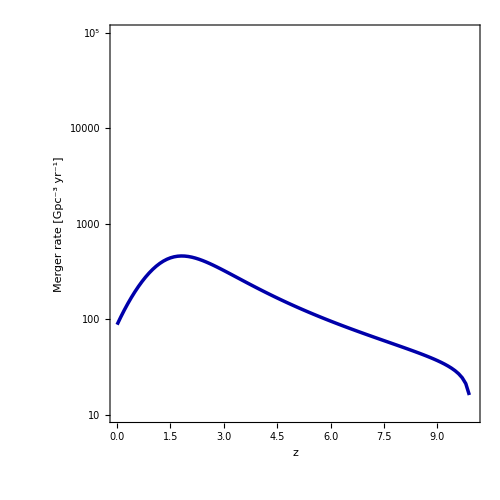

```mathematica
ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-49,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Blue],Thickness[0.005]]]
```

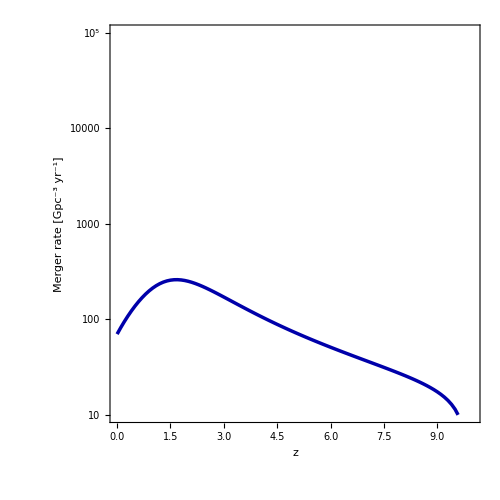

```mathematica
ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-50,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Blue],Thickness[0.005]]]
```

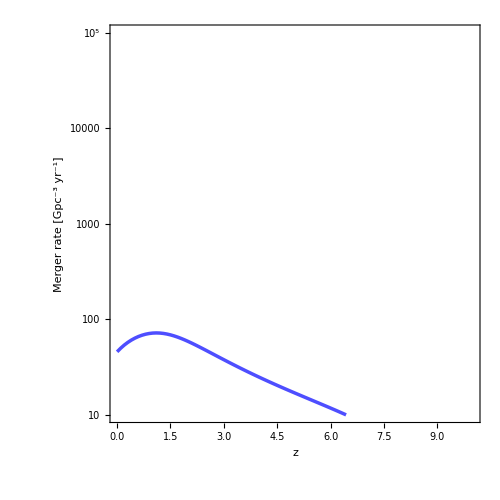

```mathematica
ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-51,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[RGBColor["#4E4EFF"],Thickness[0.005]]]
```

```mathematica
q=Join[Table[{z,10^9*mergerns[z]},{z,0,2,0.2}],Table[{z,10^9*mergerns[z]},{z,2,9,0.5}],{{9.9,10^9*mergerns[9.9]}}];
```

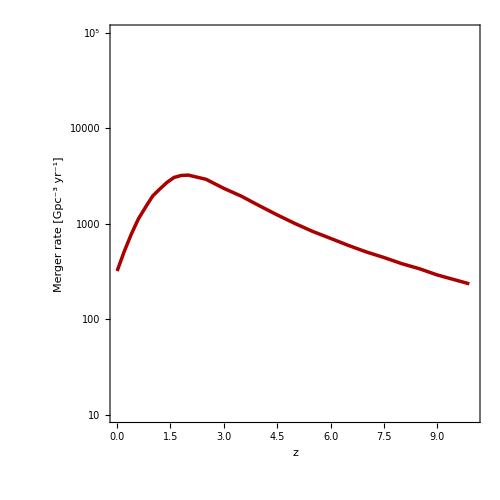

```mathematica
ListLogPlot[{Table[{q[[i,1]],q[[i,2]]},{i,1,Length[q]}]},Frame->True,Joined->True,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Red],Thickness[0.005]],PlotRangePadding->None]
```

```mathematica
t[z_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,z,∞}];(*in year*)
```

```mathematica
R[fpbh_,mpbh_,z_]:=1.6*10^6*(fpbh)^(53/37)*(1/4)^(-34/37)*2^(-32/37)*mpbh^(-32/37)*(t[z]/t[0])^(-34/37)*((5*0.01^2)/(6*0.007))^(21/74)*HypergeometricU[21/74,1/2,(5*0.01^2)/(6*0.007)];(*in Gpc^-3 yr^-1*)(*see 1812.01930, 1801.10327*)
```

```mathematica
myticks={{{{10,"10"},{20,""},{30,""},{40,""},{50,""},{60,""},{70,""},{80,""},{90,""},{100,"10^2",{0.015,0}},{200,""},{300,""},{400,""},{500,""},{600,""},{700,""},{800,""},{900,""},{1000,"10^3",{0.015,0}},{2000,""},{3000,""},{4000,""},{5000,""},{6000,""},{7000,""},{8000,""},{9000,""},{10^4,"10^4",{0.015,0}},{20000,""},{30000,""},{40000,""},{50000,""},{60000,""},{70000,""},{80000,""},{90000,""},{10^5,"10^5",{0.015,0}},{2*10^5,""},{3*10^5,""},{4*10^5,""},{5*10^5,""},{6*10^5,""},{7*10^5,""},{8*10^5,""},{9*10^5,""},{10^6,"10^6",{0.015,0}}}, {{10,""},{20,""},{30,""},{40,""},{50,""},{60,""},{70,""},{80,""},{90,""},{100,"",{0.015,0}},{200,""},{300,""},{400,""},{500,""},{600,""},{700,""},{800,""},{900,""},{1000,"",{0.015,0}},{2000,""},{3000,""},{4000,""},{5000,""},{6000,""},{7000,""},{8000,""},{9000,""},{10^4,"",{0.015,0}},{20000,""},{30000,""},{40000,""},{50000,""},{60000,""},{70000,""},{80000,""},{90000,""},{10^5,"",{0.015,0}},{2*10^5,""},{3*10^5,""},{4*10^5,""},{5*10^5,""},{6*10^5,""},{7*10^5,""},{8*10^5,""},{9*10^5,""},{10^6,"",{0.015,0}}}},{Automatic,Automatic}};
```

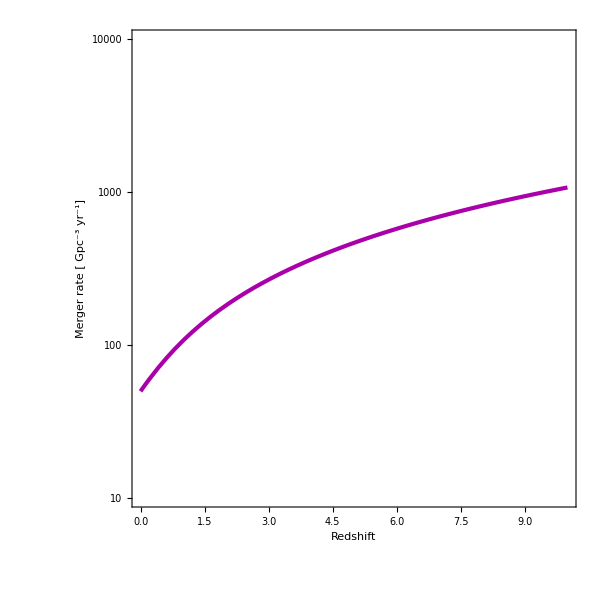

```mathematica
LogPlot[R[0.001,1.3,z],{z,0,10},Frame->True,AspectRatio->1,ImageSize->600,FrameStyle->Directive[18, "Times",Black,Thickness[0.003]],FrameTicksStyle->24,PlotRange->{{0,10},{10,10^4}},FrameTicks->myticks,FrameLabel->{Style["Redshift",FontSize->28],Style["Merger rate [ Gpc^-3 yr^-1]",FontSize->28]},PlotStyle->Directive[Darker[Magenta],Thickness[0.005]]]
```

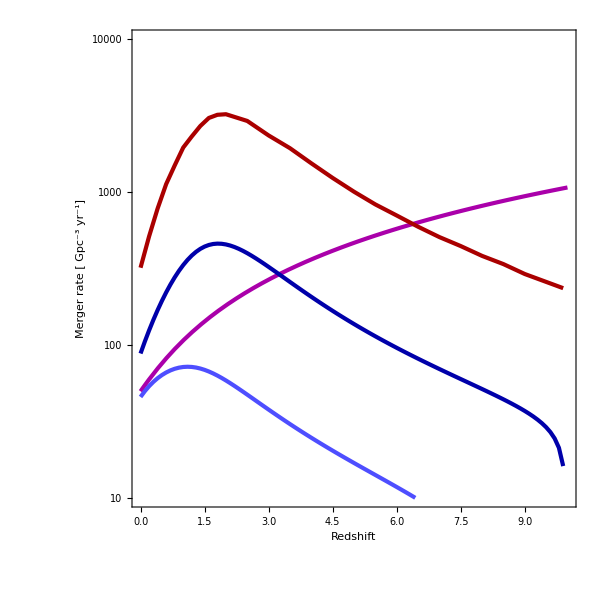

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,Graphics[Rotate[Text[Style["PBH-PBH merger",Darker[Magenta],FontSize->18],Scaled[{0.82,0.7}]],0 Degree]],Graphics[Rotate[Text[Style["NS-NS merger",Darker[Red],FontSize->18],Scaled[{0.48,0.8}]],0 Degree]],Graphics[Rotate[Text[Style["TBH-TBH merger",Darker[Blue],FontSize->18],Scaled[{0.82,0.32}]],0 Degree]],Graphics[Rotate[Text[Style["TBH-TBH merger",RGBColor["#4E4EFF"],FontSize->18],Scaled[{0.35,0.05}]],0 Degree]],Graphics[Rotate[Text[Style[" m_χ = 10^4 GeV ",Darker[Blue],FontSize->18],Scaled[{0.65,0.44}]],0 Degree]],Graphics[Rotate[Text[Style[" σ_χn = 10^-45 cm^2 ",Darker[Blue],FontSize->18],Scaled[{0.66,0.39}]],0 Degree]],Graphics[Rotate[Text[Style[" m_χ = 10^4 GeV ",RGBColor["#4E4EFF"],FontSize->18],Scaled[{0.50,0.23}]],0 Degree]],Graphics[Rotate[Text[Style[" σ_χn = 10^-47 cm^2 ",RGBColor["#4E4EFF"],FontSize->18],Scaled[{0.51,0.18}]],0 Degree]]]
```

```mathematica
dh=(3*10^8)/(70.4*1/(3.086*10^19))*3.24*10^-23;(*in Mpc*)
```

```mathematica
dc[z_]:=dh*NIntegrate[1/((0.73+0.27*(1+p)^3)^0.5),{p,0,z}];(*in Mpc*)
```

```mathematica
dL[z_]:=(1+z)*dc[z];
```

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet
```

0.796457

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet
```

0.402547

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet
```

6173.08

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet
```

1900.27

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet
```

0.

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet
```

0.

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet
```

983.471

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet
```

190.004

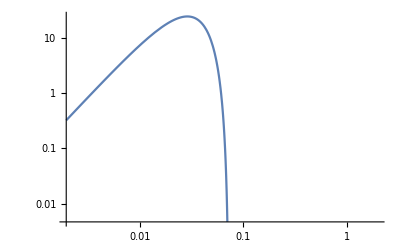

```mathematica
LogLogPlot[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2}]
```

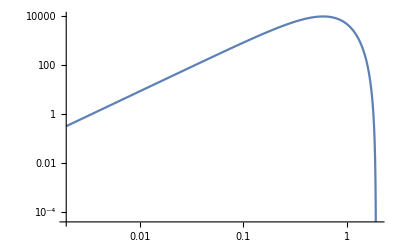

```mathematica
LogLogPlot[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2}]
```

```mathematica
(*PBH*)
```

```mathematica
t[z_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,z,∞}];(*in year*)
```

```mathematica
R[fpbh_,mpbh_,z_]:=1.6*10^6*(fpbh)^(53/37)*(1/4)^(-34/37)*2^(-32/37)*mpbh^(-32/37)*(t[z]/t[0])^(-34/37)*((5*0.01^2)/(6*0.007))^(21/74)*HypergeometricU[21/74,1/2,(5*0.01^2)/(6*0.007)];(*in Gpc^-3 yr^-1*)(*see 1812.01930, 1801.10327*)
```

```mathematica
dh=(3*10^8)/(70.4*1/(3.086*10^19))*3.24*10^-23;(*in Mpc*)
```

```mathematica
dc[z_]:=dh*NIntegrate[1/((0.73+0.27*(1+p)^3)^0.5),{p,0,z}];(*in Mpc*)
```

```mathematica
dL[z_]:=(1+z)*dc[z];
```

```mathematica
(*NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*(10^-9*R[0.001522,1.3,z])/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet(*for aLIGO*)*)
```

```mathematica
(*NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*(10^-9*R[0.001522,1.3,z])/(1+z)*If[0≤ ( dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet(*for aLIGO*)*)
```

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*(10^-9*R[0.0019665,1.3,z])/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet(*for ET*)
```

6172.99

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*(10^-9*R[0.0019665,1.3,z])/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet(*for ET*)
```

821.393

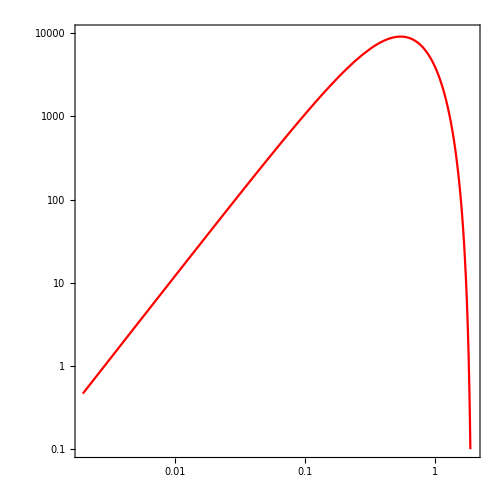

```mathematica
LogLogPlot[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*(10^-9*R[0.001909,1.3,z])/(1+z)*If[0≤( dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/1.16)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,2},Frame->True,ImageSize->500,AspectRatio->1,PlotRange->{Automatic,{0.1,10000}},PlotStyle->Red]
```

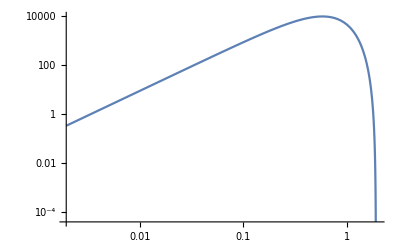
```mathematica
Show[-Graphics-,-Graphics-]
```

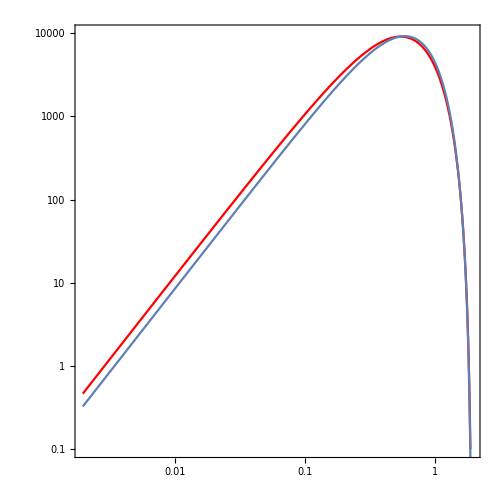

```mathematica
(*NS-NS merger rate with redshift*)(*Taylor et al.*)(*1.0 Solar mass Neutron Star*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.6*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
tage=6.69*10^9*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27);
Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
NchFermion[mx_?NumericQ]:=Mpl^3/mx^3;
```

```mathematica
GN=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
cns=0.17;
λ=0.25;
```

```mathematica
mcrit=1/GN*(cns^3/(74*π*4*π*λ*ρ*5.62*10^26*(1.98*10^-16)^3))^0.25;(*critical mass for BH evaporation in GeV*)
```

```mathematica
mcrit
```

2.71619×10^37

```mathematica
τcollapse[mx_?NumericQ,T_?NumericQ]:=cns^3/(4*π*λ*ρ*10^-3*5.62*10^23*(1.98*10^-14)^3*GN^2*mx*Max[Nself[mx,T],NchBoson[mx]])*6.58*10^-25*1/(3.15*10^7);(*in year, time required to consume the host star*)
```

```mathematica
τtrans[ρ_?NumericQ,mx_?NumericQ,T_?NumericQ,sigma_?NumericQ]:=1/(ρ/0.4*auni[mx,sigma])*Max[Nself[mx,T],NchBoson[mx]]*1/(3.15*10^7)+τcollapse[mx,T];
(*in year, time required to transmute, first term presents time required to capture enough DM particles to achieve the BH foramtion criterion, second term presents time required to consume the host star*)
```

```mathematica
τtrans[1000,10^4,2.1*10^6,10^-49]
```

5.79864×10^6

```mathematica
tage*1/(3.15*10^7)//N
```

6.69×10^9

```mathematica
Max[Nself[10^4,2.1*10^6],NchBoson[10^4]]
```

4.59708×10^38

```mathematica
1000/0.4*totcapuni[10^4,10^-49]
```

5.30376×10^41

```mathematica
t[z_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,z,∞}];(*in year*)
```

```mathematica
tstar=t[10]
```

4.88599×10^8

```mathematica
f[zb_]:=NIntegrate[1/((1+p)*70.4*1/(3.086*10^19)*3.154*10^7*(0.73+0.27*(1+p)^3)^0.5),{p,zb,∞}];
```

```mathematica
p1=Table[{i*10^9,zb/.FindRoot[f[zb]==i*10^9,{zb,0}]},{i,0.01,13.79,0.01}];//Quiet
```

```mathematica
f1=Interpolation[Table[{p1[[i,1]],p1[[i,2]]},{i,1,Length[p1]}]];
```

```mathematica
mergerns[z_]:=320/1124.55*If[tstar≤ t[z],NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,t[z]}],0]//Quiet
```

```mathematica
ρc[z_]=1.05*10^-5*0.704^2*(0.73+0.27*(1+z)^3);(*in GeV/cm^3*)
```

```mathematica
c200=13.31;

m200=0.82*10^12*2*10^33*5.62*10^23;(*in GeV*)
```

```mathematica
rs[z_]:=(m200/(4/3*π*c200^3*200*ρc[z]))^(1/3)*1/(3.086*10^21);(*in kpc*)
```

```mathematica
rs[0]
```

14.5034

```mathematica
ρs[z_]:=m200/(4*π*rs[z]^3*(3.086*10^21)^3*(Log[1+c200]-c200/(1+c200)));(*in GeV/cm^3*)
```

```mathematica
ρNFW[r_,z_]:=ρs[z]/(r/rs[z]*(1+r/rs[z])^2);(*DM density at GeV/cm^3 for NFW profile at various redshifts*)
```

```mathematica
ρNFW[8.5,0]
```

0.320571

```mathematica
mergertrans1[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.01,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.015,z],mx,T,sigma])}],0];(*merger rate assuming the NS are at 0.01-0.02 kpc*)(*in Mpc^-3 yr^-1*)
```

```mathematica
mergertrans2[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.02,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.025,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans3[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.03,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.035,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans4[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.04,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.045,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans5[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.05,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.055,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans6[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.06,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.065,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans7[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.07,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.075,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans8[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.08,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.085,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans9[mx_,T_,sigma_,z_]:=If[tstar≤ (t[z]-τtrans[ρNFW[0.09,z],mx,T,sigma]),NIntegrate[0.015*10^-5*(1+f1[tb])^2.7/(1+((1+f1[tb])/2.9)^5.6)*1/(t[z]-tb)*1/Log[t[z]/(50*10^6)],{tb,tstar,(t[z]-τtrans[ρNFW[0.095,z],mx,T,sigma])}],0];
```

```mathematica
mergertrans[mx_,T_,sigma_,z_]:=1/9*320/1124.55*(mergertrans1[mx,T,sigma,z]+mergertrans2[mx,T,sigma,z]+mergertrans3[mx,T,sigma,z]+mergertrans4[mx,T,sigma,z]+mergertrans5[mx,T,sigma,z]+mergertrans6[mx,T,sigma,z]+mergertrans7[mx,T,sigma,z]+mergertrans8[mx,T,sigma,z]+mergertrans9[mx,T,sigma,z]);
```

```mathematica
((1.0*1.0)^(3/5)/(1.0+1.0)^(1/5))^(6/5)
```

0.846745

```mathematica
mergerns[0]*10^9
```

320.

```mathematica
(*ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-49,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Blue],Thickness[0.005]]]*)
```

```mathematica
(*ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-50,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Blue],Thickness[0.005]]]*)
```

```mathematica
(*ListLogPlot[{Table[{z,10^9*mergertrans[10^4,2.1*10^6,10^-51,z]},{z,0,10,0.1}]},Frame->True,Joined->True,InterpolationOrder->1,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[RGBColor["#4E4EFF"],Thickness[0.005]]]*)
```

```mathematica
(*q=Join[Table[{z,10^9*mergerns[z]},{z,0,2,0.2}],Table[{z,10^9*mergerns[z]},{z,2,9,0.5}],{{9.9,10^9*mergerns[9.9]}}];*)
```

```mathematica
(*ListLogPlot[{Table[{q[[i,1]],q[[i,2]]},{i,1,Length[q]}]},Frame->True,Joined->True,AspectRatio->1,ImageSize->500,PlotRange->{{0,10},{10,10^5}},FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->20],Style["Merger rate [Gpc^-3 yr^-1]",FontSize->20]},PlotStyle->Directive[Darker[Red],Thickness[0.005]],PlotRangePadding->None]*)
```

```mathematica
dh=(3*10^8)/(70.4*1/(3.086*10^19))*3.24*10^-23;(*in Mpc*)
```

```mathematica
dc[z_]:=dh*NIntegrate[1/((0.73+0.27*(1+p)^3)^0.5),{p,0,z}];(*in Mpc*)
```

```mathematica
dL[z_]:=(1+z)*dc[z];
```

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet
```

0.357885

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet
```

0.165411

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet
```

3085.27

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,0,1}]//Quiet
```

868.099

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet
```

0.

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤ ( dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/80*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet
```

0.

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-49,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet
```

35.5414

```mathematica
NIntegrate[(4*π*dc[z]^2*dh)/((0.73+0.27*(1+z)^3)^0.5)*mergertrans[10^4,2.1*10^6,10^-51,z]/(1+z)*If[0≤( dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))≤ 4,((1+dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))*(4-dL[z]/1591*(1.2/0.85)^(5/6)/(1+z)^(5/6))^4)/256,0],{z,1,3}]//Quiet
```

5.84218